```mathematica
NotebookEvaluate["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/00_SplinePack-034.nb"]  // Quiet;

Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/TP_ImProc_01-m101.wl"]] //Quiet;

Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/TP_ImProc_01-m101.wl"]] //Quiet;

Clear[SavitzkyGolayFilterExtended]


SavitzkyGolayFilterExtended[DOrder_,M_,nl_,nr_,data_] := Module[{i,j,p,t},
p = Table[t^i,{i,0,M}];
j = nl+nr+1;
i = Range[j];
Join[
D[Fit[Transpose[{i,Take[data,   j]}],p,t],{t,DOrder}]/.t->Take[i,  nl],
SavitzkyGolayFilter[DOrder,M,nl,nr,data],
D[Fit[Transpose[{i,Take[data,-j]}],p,t],{t,DOrder}]/.t->Take[i,-nr]]];



Clear[
ParamPadToTake,
ParamTakeToPad]


ParamPadToTake[ImgDim_,LeftRightBottomTop_] := {
{LeftRightBottomTop[[2,2]]+1,If[ListQ[ImgDim],ImgDim[[2]],-1]-LeftRightBottomTop[[2,1]]},
{LeftRightBottomTop[[1,1]]+1,If[ListQ[ImgDim],ImgDim[[1]],-1]-LeftRightBottomTop[[1,2]]}};


ParamTakeToPad[ImgDim_,RowsCols_] := Module[{LeftRightBottomTop},
LeftRightBottomTop = Reverse[RowsCols];
LeftRightBottomTop = Transpose[LeftRightBottomTop];
LeftRightBottomTop[[1]] -= 1;
LeftRightBottomTop[[2]] = ImgDim-LeftRightBottomTop[[2]];
LeftRightBottomTop = Transpose[LeftRightBottomTop];
LeftRightBottomTop[[2]] = Reverse[LeftRightBottomTop[[2]]];
LeftRightBottomTop];



Clear[
LoadFromTIF,
SaveAsTIF]


LoadFromTIF[CheckBitLength_,fname_] := Module[{X},
X = Import[fname];
X[[-1]] = ReadQRCode[X[[-1]]];
If[
If[TrueQ[CheckBitLength],
SameQ[
Piecewise[{{1,#≤1},{8,1<#≤8}},16]&/@Ceiling[Log[2,X[[-1,1]]]],
Ceiling[Log[2,Map[Length[Union@@ImageData[#]]&,Drop[X,-1]]]]],
True],
X[[-1]] = X[[-1,2]];
Fold[
ReplacePart[#1,#2[[1]],#2[[2]]]&,
X[[-1]],
Transpose[
{Drop[X,-1],
Position[X[[-1]],Image]}]]]];


SaveAsTIF[fname_,data_] := Module[{x,X},
X = data/.x_:>MyVectorPlaceholder/;ImageQ[x];
X = Append[
Extract[data,Position[X,MyVectorPlaceholder]],
X/.MyVectorPlaceholder->Image];
X[[-1]] = {Map[Length[Union@@ImageData[#]]&,Drop[X,-1]],X[[-1]]};
X[[-1]] = WriteQRCode[X[[-1]]];
MDExport[fname,X,"ImageEncoding"->"LZW"]];



Clear[ChangeImgDims]


ChangeImgDims[
  B_?ImageQ,
nx_?IntegerQ,
ny_?IntegerQ,
padding_] := Module[{R,x,y},
{x,y} = {nx,ny}-ImageDimensions[R=B];
If[y<0,
y = {Quotient[-y,2],-y};
y = {First[y],Subtract@@y}+{1,-1};
R = ImageTake[R,y],
If[y>0,
y = {y,Quotient[y,2]};
y = {Last[y],Subtract@@y};
R = ImagePad[R,{{0,0},y},padding]]];
If[x<0,
x = {Quotient[-x,2],-x};
x = {First[x],Subtract@@x}+{1,-1};
R = ImageTake[R,All,x],
If[x>0,
x = {x,Quotient[x,2]};
x = {Last[x],Subtract@@x};
R = ImagePad[R,{x,{0,0}},padding]]];
R];
```

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

```mathematica
$HistoryLength = 10;
```

```mathematica
PrependTo[MyTS,FontSize->24];
```

```mathematica
DatenOrdner = NotebookDirectory[]~~"output directory\\"
```

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\

```mathematica
Clear[ToEnglish,Z]
```

```mathematica
{ToEnglish,Z} = Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/EmissionRatePlotData.dat"]];
```

```mathematica
TableForm[Z]
Length[Z]
```

Proband | Instrument | Task | Begin (s) | End (s) | Emission rate (P/s) | ER σ (P/s) | Water emission (mg/s) | Particles/Water (P/mg)
 |  |  |  |  |  |  |  | 
C2 | C | Breathing | 6206 | 7408 | -98 | 171 | 6.35133 | -15.4298
C2 | C | Playing | 1200 | 2408 | 355 | 261 | 19.6555 | 18.0611
C2 | C | Playing With Surgical Mask | 8449 | 9061 | 790 | 764 | 7.36465 | 107.269
C2 | C | Speaking | 4010 | 5236 | 22 | 100 | 8.70055 | 2.52858
S1 | S | Breathing | 3340 | 4555 | 228 | 153 |  | 
S1 | S | Speaking | 1200 | 2405 | 89 | 94 |  | 
S1 | S | Speaking With Surgical Mask | 5466 | 6682 | -122 | 196 |  | 
S2 | S | Speaking With Surgical Mask | 4524 | 5723 | -1 | 184 | 4.8826 | -0.204809
S3 | S | Breathing | 4051 | 5256 | -157 | 302 | 8.03068 | -19.55
S3 | S | Speaking | 7443 | 8659 | 590 | 162 | 5.92732 | 99.5391
S3 | S | Speaking With Surgical Mask | 1200 | 2408 | 666 | 215 | 5.7454 | 115.919
S4 | S | Speaking | 5299 | 6523 | -137 | 198 | 5.18286 | -26.4333
S4 | S | Speaking With Surgical Mask | 424 | 1648 | 78 | 93 | 6.08984 | 12.8082
S5 | S | Speaking With Surgical Mask | 876 | 2098 | -50 | 107 | 5.95228 | -8.40014
S6 | S | Breathing | 4106 | 5320 | -199 | 335 | 8.3125 | -23.9398
S6 | S | Speaking | 1869 | 3080 | 16 | 189 | 17.5803 | 0.910107
S6 | S | Speaking With Surgical Mask | 6825 | 8040 | 114 | 267 | 5.6046 | 20.3404
S7 | S | Breathing | 3261 | 4466 | -105 | 151 | 3.11025 | -33.7593
S7 | S | Speaking | 5840 | 7058 | -260 | 312 | 5.79921 | -44.8337
S7 | S | Speaking With Surgical Mask | 1200 | 2405 | 473 | 83 | 6.94787 | 68.0784
S8 | S | Breathing | 3646 | 4851 | 48 | 164 | 3.95646 | 12.1321
S8 | S | Speaking | 7694 | 8906 | 203 | 327 | 4.58863 | 44.2398
S8 | S | Speaking With Surgical Mask | 1200 | 2440 | -163 | 249 | 9.10583 | -17.9006
S9 | S | Breathing | 3656 | 4859 | 455 | 302 | 8.05346 | 56.4975
S9 | S | Speaking | 7093 | 8303 | 1605 | 305 | 8.3908 | 191.281
S9 | S | Speaking With Surgical Mask | 1200 | 2403 | 586 | 610 | 10.1777 | 57.5767
S10 | S | Breathing | 4239 | 5441 | 296 | 224 | 8.28801 | 35.7142
S10 | S | Playing | 10644 | 11848 | 2122 | 605 | 12.8713 | 164.863
S10 | S | Speaking | 7057 | 8273 | 242 | 209 | 8.4451 | 28.6557
S10 | S | Speaking With Surgical Mask | 1200 | 2408 | 947 | 475 | 18.7504 | 50.5057
S11 | S | Breathing | 3418 | 4622 | 559 | 443 | 9.5607 | 58.4685
S11 | S | Speaking | 5828 | 7040 | 1671 | 207 | 9.96255 | 167.728
S11 | S | Speaking With Surgical Mask | 944 | 2159 | 2 | 413 | 9.34569 | 0.214002
S12 | S | Breathing | 4027 | 5230 | -44 | 210 | 12.5258 | -3.51274
S12 | S | Playing | 10374 | 11579 | 1355 | 428 | 16.1923 | 83.682
S12 | S | Speaking | 7275 | 8480 | 481 | 229 | 8.78184 | 54.7721
S12 | S | Speaking With Surgical Mask | 1093 | 2317 | 970 | 160 | 16.4966 | 58.8001
O2 | O | Breathing | 6157 | 7360 | -48 | 198 | 5.04529 | -9.51383
O2 | O | Playing | 1828 | 3032 | 838 | 288 | 19.4271 | 43.1356
O2 | O | Playing With Surgical Mask | 8546 | 9159 | 320 | 568 | 8.02528 | 39.874
O2 | O | Speaking | 4113 | 5328 | -245 | 356 | 8.90999 | -27.4972
O3 | O | Breathing | 5900 | 7104 | 23 | 166 | 5.18188 | 4.43854
O3 | O | Playing | 1200 | 2400 | 466 | 115 | 21.9253 | 21.254
O3 | O | Playing With Surgical Mask | 8292 | 8912 | 215 | 400 | 9.70404 | 22.1557
O3 | O | Speaking | 3515 | 4735 | 56 | 307 | 8.71046 | 6.42905
O3 | O | Speaking With Surgical Mask | 10570 | 11789 | -164 | 273 | 4.28641 | -38.2605
O4 | O | Breathing | 6226 | 7429 | 93 | 95 | 5.80198 | 16.029
O4 | O | Playing | 1200 | 2427 | 1309 | 210 | 16.382 | 79.9047
O4 | O | Playing With Surgical Mask | 8482 | 9086 | 911 | 612 | 6.44717 | 141.302
O4 | O | Speaking | 3697 | 4929 | 189 | 114 | 6.88974 | 27.4321
O4 | O | Speaking With Surgical Mask | 10224 | 11456 | -66 | 142 | 4.88131 | -13.521
O5 | O | Speaking | 3109 | 4303 | -164 | 319 | 11.3842 | -14.4059
O6 | O | Breathing | 6070 | 7281 | 117 | 304 | 9.31335 | 12.5626
O6 | O | Playing | 1200 | 2429 | 521 | 316 | 35.627 | 14.6238
O6 | O | Playing With Surgical Mask | 8842 | 9451 | 1610 | 483 | 9.25584 | 173.944
O6 | O | Speaking | 3683 | 4905 | 257 | 227 | 14.3611 | 17.8955
O7 | O | Breathing | 6229 | 7432 | 181 | 223 | 9.50645 | 19.0397
O7 | O | Playing | 1200 | 2433 | 2535 | 195 | 34.9787 | 72.4727
O7 | O | Playing With Surgical Mask | 8409 | 9017 | 670 | 238 | 13.4193 | 49.9282
O7 | O | Speaking | 3689 | 4894 | 715 | 296 | 18.8318 | 37.9676
O8 | O | Breathing | 7834 | 9039 | -187 | 432 | 7.19722 | -25.9823
O8 | O | Playing | 1569 | 2777 | 1229 | 147 | 32.4661 | 37.8549
O8 | O | Playing With Surgical Mask | 10204 | 10835 | 1053 | 273 | 15.7934 | 66.6734
O8 | O | Speaking | 5280 | 6512 | -175 | 294 | 9.94692 | -17.5934
O9 | O | Breathing | 6075 | 7278 | -145 | 266 | 5.34168 | -27.145
O9 | O | Playing | 1200 | 2404 | 1645 | 461 | 22.9649 | 71.6312
O9 | O | Playing With Surgical Mask | 8431 | 9042 | 1589 | 534 | 14.8384 | 107.087
O9 | O | Speaking | 4015 | 5222 | 9 | 191 | 7.94626 | 1.13261
O10 | O | Playing | 1200 | 2402 | 218 | 185 | 17.797 | 12.2493
O10 | O | Playing With Surgical Mask | 8608 | 9211 | -209 | 268 | 17.5343 | -11.9195
O10 | O | Speaking | 3747 | 4961 | -3 | 148 | 11.8492 | -0.253182
O10 | O | Speaking With Surgical Mask | 10242 | 11447 | -136 | 279 | 10.1543 | -13.3933
O11 | O | Breathing | 5645 | 6848 | 21 | 244 | 7.20408 | 2.91501
O11 | O | Playing | 1032 | 2258 | 1484 | 211 | 26.5107 | 55.9774
O11 | O | Playing With Surgical Mask | 8124 | 8741 | 1263 | 1224 | 10.8125 | 116.809
O11 | O | Speaking | 3379 | 4595 | 144 | 409 | 13.1723 | 10.932
O12 | O | Breathing | 6274 | 7483 | -150 | 196 | 8.32992 | -18.0074
O12 | O | Playing | 1200 | 2411 | 660 | 274 | 24.5285 | 26.9075
O12 | O | Playing With Surgical Mask | 8782 | 9386 | 894 | 620 | 14.5733 | 61.3453
O12 | O | Speaking | 3565 | 4770 | 725 | 128 | 12.7055 | 57.0621
F1 | F | Breathing | 5183 | 6376 | 48 | 35 | 6.17609 | 7.7719
F1 | F | Playing | 1200 | 2392 | 1434 | 366 | 26.468 | 54.1787
F1 | F | Speaking | 3057 | 4260 | 641 | 384 | 11.7497 | 54.5544
F1 | F | Speaking With Surgical Mask | 6929 | 8125 | 447 | 189 | 8.23895 | 54.2545
F2 | F | Breathing | 6063 | 7278 | 119 | 151 | 7.49066 | 15.8865
F2 | F | Playing | 1379 | 2586 | 343 | 486 | 29.3035 | 11.7051
F2 | F | Speaking | 3612 | 4826 | 63 | 92 | 14.9865 | 4.20379
F3 | F | Breathing | 3293 | 4493 | 39 | 213 |  | 
F3 | F | Playing | 1588 | 2755 | 57 | 175 |  | 
F3 | F | Speaking | 4983 | 6228 | -144 | 175 |  | 
F3 | F | Speaking With Surgical Mask | 7425 | 8615 | 455 | 293 |  | 
F4 | F | Breathing | 5604 | 6813 | -2 | 317 | 8.18271 | -0.244418
F4 | F | Playing | 1200 | 2405 | 2318 | 644 | 27.4037 | 84.587
F4 | F | Speaking | 3543 | 4759 | -79 | 366 | 13.6893 | -5.77093
F4 | F | Speaking With Surgical Mask | 7928 | 9141 | 432 | 245 | 6.09656 | 70.8597
F5 | F | Playing | 1200 | 2401 | 1143 | 206 | 21.095 | 54.1834
F5 | F | Speaking | 4001 | 5223 | -80 | 174 | 6.67978 | -11.9764
F5 | F | Speaking With Surgical Mask | 8298 | 9499 | -89 | 291 | 5.70864 | -15.5904
F6 | F | Breathing | 4996 | 6211 | 350 | 175 | 12.8319 | 27.2759
F6 | F | Playing | 1200 | 2416 | 635 | 128 |  | 
F6 | F | Speaking | 3159 | 4364 | 7 | 67 | 23.5479 | 0.297266
F7 | F | Breathing | 5401 | 6604 | -1 | 79 |  | 
F7 | F | Playing | 1200 | 2420 | 1171 | 176 |  | 
F7 | F | Speaking | 3399 | 4611 | 129 | 256 |  | 
F7 | F | Speaking With Surgical Mask | 7200 | 8407 | 486 | 220 |  | 
F9 | F | Breathing | 5911 | 7119 | 274 | 317 | 4.31308 | 63.5277
F9 | F | Playing | 1200 | 2404 | 799 | 307 | 8.14177 | 98.1359
F9 | F | Speaking | 3521 | 4759 | -121 | 140 | 5.55579 | -21.7791
F9 | F | Speaking With Surgical Mask | 8075 | 9283 | 474 | 368 | 5.38106 | 88.0868
F10 | F | Playing | 1200 | 2398 | 11 | 288 |  | 
F10 | F | Speaking | 3145 | 4340 | 5 | 203 | 18.3802 | 0.272032
F10 | F | Speaking With Surgical Mask | 6889 | 8093 | 943 | 173 | 5.75107 | 163.97
F11 | F | Breathing | 5914 | 7118 | 149 | 368 | 3.98727 | 37.3689
F11 | F | Playing | 1200 | 2413 | 15 | 313 | 18.7977 | 0.797972
F12 | F | Breathing | 5897 | 7103 | -127 | 237 | 6.85545 | -18.5254
F12 | F | Playing | 1160 | 2375 | 1708 | 348 | 29.6123 | 57.6787
F12 | F | Speaking | 3754 | 4965 | 251 | 163 | 10.3012 | 24.3661
F12 | F | Speaking With Surgical Mask | 8233 | 9443 | 564 | 295 | 6.65816 | 84.7081
F13 | F | Playing | 1095 | 2307 | 905 | 75 | 12.3282 | 73.409
F13 | F | Speaking | 3354 | 4557 | 228 | 191 | 9.82398 | 23.2085
F13 | F | Speaking With Surgical Mask | 8378 | 9576 | 88 | 239 | 5.65073 | 15.5732
F14 | F | Breathing | 6529 | 7740 | 181 | 209 | 3.6099 | 50.14
F14 | F | Playing | 1200 | 2425 | 700 | 368 | 13.7627 | 50.862
F14 | F | Speaking | 3939 | 5168 | 64 | 253 | 7.93103 | 8.06957
F15 | F | Breathing | 6108 | 7316 | -11 | 196 | 4.08124 | -2.69526
F15 | F | Playing | 1200 | 2404 | 2358 | 120 | 24.8061 | 95.0573
F15 | F | Speaking | 3849 | 5063 | 233 | 215 | 9.1381 | 25.4976
F15 | F | Speaking With Surgical Mask | 8331 | 9540 | 31 | 316 | 4.55566 | 6.80472
F16 | F | Breathing | 6620 | 7824 | 200 | 83 | 6.77415 | 29.524
F16 | F | Playing | 1200 | 2409 | 364 | 278 | 33.7478 | 10.7859
F16 | F | Speaking | 4532 | 5738 | 298 | 187 | 12.2373 | 24.3518
F17 | F | Breathing | 6635 | 7852 | 21 | 124 | 3.95503 | 5.3097
F17 | F | Playing | 1200 | 2418 | 512 | 294 | 17.1398 | 29.872
F17 | F | Speaking | 4614 | 5820 | 410 | 161 | 6.47669 | 63.3039
F17 | F | Speaking With Surgical Mask | 9133 | 10355 | 1125 | 161 | 4.30338 | 261.423
F18 | F | Breathing | 6927 | 8129 | 86 | 191 | 5.96245 | 14.4236
F18 | F | Playing | 1516 | 2727 | 390 | 155 | 19.7321 | 19.7648
F18 | F | Speaking | 4058 | 5259 | 427 | 123 | 11.2176 | 38.0651
F18 | F | Speaking With Surgical Mask | 9464 | 10668 | 513 | 395 | 8.31043 | 61.7296
F19 | F | Breathing | 6116 | 7321 | 589 | 354 | 5.46943 | 107.689
F19 | F | Playing | 1200 | 2423 | 1917 | 365 | 8.88526 | 215.751
F19 | F | Speaking | 3664 | 4888 | 681 | 151 | 2.84054 | 239.743
F19 | F | Speaking With Surgical Mask | 9035 | 10245 | 776 | 531 | 3.76071 | 206.344
F20 | F | Breathing | 6432 | 7665 | 204 | 140 | 3.8381 | 53.1514
F20 | F | Playing | 1200 | 2403 | 1410 | 342 | 13.9815 | 100.848
F20 | F | Speaking | 3807 | 5022 | 770 | 152 | 5.98523 | 128.65
F20 | F | Speaking With Surgical Mask | 8636 | 9874 | 559 | 162 | 5.27915 | 105.888
T1 | T | Playing | 1200 | 2415 | 192 | 448 | 30.0835 | 6.38223
T1 | T | Playing With Surgical Mask | 8984 | 9589 | 28 | 2562 | 9.06738 | 3.08799
T1 | T | Speaking | 3907 | 5135 | -306 | 348 | 13.4608 | -22.7327

152

```mathematica
Entries[Z,"Instrument"]
```

{{67,F},{43,O},{33,S},{4,C},{3,T}}

```mathematica
Entries[Z,"Aufgabe"/.ToEnglish]
```

{{41,Speaking},{35,Breathing},{33,Playing},{29,Speaking With Surgical Mask},{12,Playing With Surgical Mask}}

```mathematica
Measurements = {"Atmen","Sprechen mit MNS","Sprechen","Musikspiel mit Schutz","Musikspiel"}/.ToEnglish;
TableForm[Subsets[Measurements,{2}]]
```

Breathing | Speaking With Surgical Mask
Breathing | Speaking
Breathing | Playing With Surgical Mask
Breathing | Playing
Speaking With Surgical Mask | Speaking
Speaking With Surgical Mask | Playing With Surgical Mask
Speaking With Surgical Mask | Playing
Speaking | Playing With Surgical Mask
Speaking | Playing
Playing With Surgical Mask | Playing

```mathematica
OutPath = StringJoin[DatenOrdner,"Fig\\"]
```

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\

Creating new directory  C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-s

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-s\Playing With Surgical Mask.tif

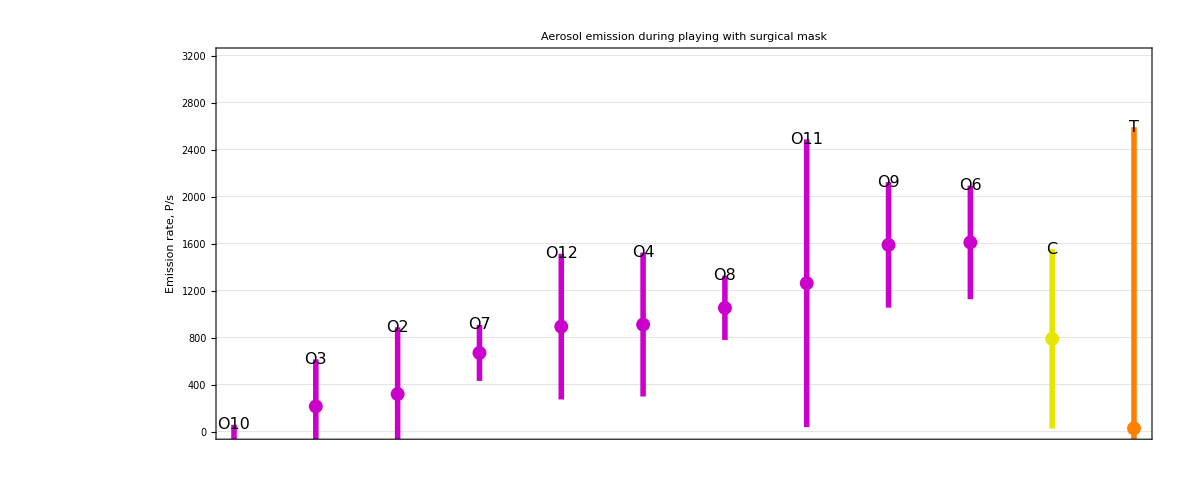

```mathematica
Clear[R,TaskPlot,
A,h,i]

R = {-600*0,3000+200};

TaskPlot[task_?StringQ] := Module[{A,h,i},
A = SelectRows[Z,"Aufgabe"/.ToEnglish,(#==task)&];
If[Length[A]==2,Return[1]];
A = Drop[ExtractColumn[A,{"Instrument","Emissionsrate (P/s)","ER σ (P/s)","Proband"}/.ToEnglish],2];
A = Transpose[MyPartition[1,A]];
A = Insert[A,
A[[1]]/.({
"Qu"->CMYKColor[1,0,0,0.2],
"Ob"->CMYKColor[0,1,0,0.2],
"KP"->CMYKColor[0,0,0,0.3],
"Kl"->CMYKColor[0,0,1,0.1],
"Tr"->CMYKColor[0,0.5,1,0]}/.ToEnglish),
2];
A[[1]] = A[[1]]/.({"Kl"->3,"KP"->5,"Ob"->2,"Qu"->1,"Tr"->4}/.ToEnglish);
A = Transpose[A];

A = Select[A,(#[[1]]≤4)&];
A = A/.{
"C2"->"C",
"T1"->"T"};

A = Rest/@SortBy[A,First];
A = Transpose[A];
i = 0;
A[[2]] = Map[
Flatten[
Map[(
++i;
{Point[{i,#[[1]]}],
Line[h={
{i,Max[-Infinity,#[[1]]-#[[2]]]},
{i,                                  #[[1]]+#[[2]]  }}],
Text@@Prepend[
If[MemberQ[{ (* "Playing" *) },task],
{h[[1]],{0,   2}},
{h[[2]],{0,-2}}],
Style[
StringDrop[#[[3]],0],
FontColor->GrayLevel[0],
FontFamily->"Arial",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->Round[(FontSize/.MyTS)*2/3]]]}
)&,
SortBy[#,First]]
]&,A[[2]]];
A = Flatten/@Transpose[A];
A = Graphics[
{AbsoluteThickness[  4],
AbsolutePointSize[10],
A},
AspectRatio->0.4,
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{None,"Emission rate,  P/s"/.ToEnglish},
FrameTicks->{None,Automatic},
GridLines  ->{None,Automatic},
ImageSize->1200,
LabelStyle->MyTS,
PlotLabel->StringJoin["Aerosol emission during ",ToLowerCase[task]],
PlotRange->{All,R},
PlotRangeClipping->True];


Print[
MDExport[
StringJoin[OutPath,"TaskPlots\\P-s\\",task,".tif"],
Rasterize[A],
"ImageEncoding"->"LZW"]];
A];


TaskPlot[{"Musikspiel","Musikspiel mit Schutz"}[[2]]/.ToEnglish]
```

```mathematica
TaskPlot/@(Measurements/.ToEnglish);
```

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-s\Breathing.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-s\Speaking With Surgical Mask.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-s\Speaking.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-s\Playing With Surgical Mask.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-s\Playing.tif

#### all output of figures in https://github.com/Carl-Firle/my-data-storage/tree/main/data/2020_aerosol-wind-instruments/Fig

Creating new directory  C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\mg-s

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\mg-s\Playing_Water.tif

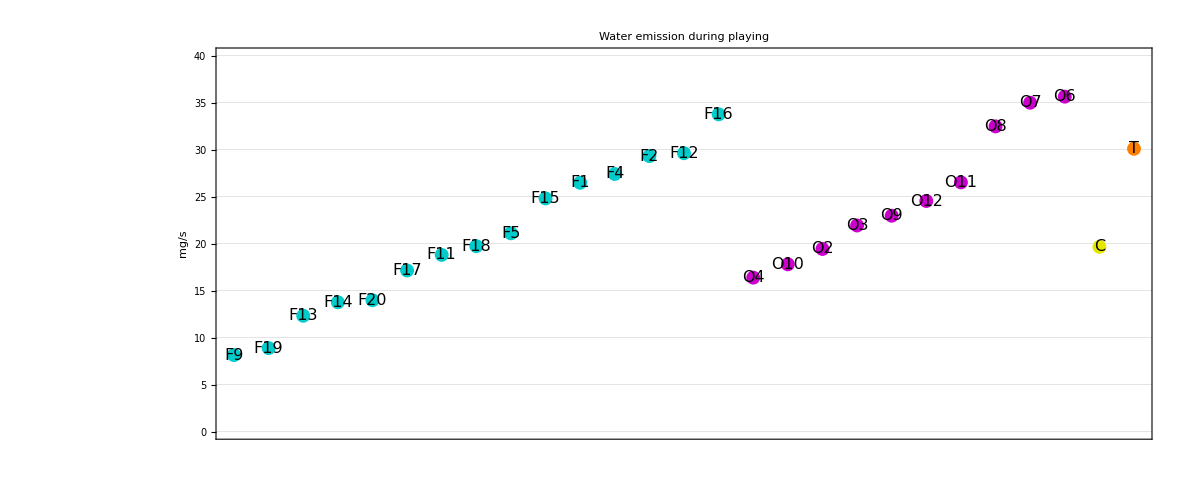

```mathematica
Clear[R,TaskPlotWater,
A,i]

R = 40;

TaskPlotWater[task_?StringQ] := Module[{A,i},
A = SelectRows[Z,"Aufgabe"/.ToEnglish,(#==task)&];
If[Length[A]==2,Return[1]];
A = Drop[ExtractColumn[A,{"Instrument","Wasseremission (mg/s)","Proband"}/.ToEnglish],2];
A = Select[A,NumericQ[#[[2]]]&];
If[A=={},Return[2]];
A = Transpose[MyPartition[1,A]];
A = Insert[A,
A[[1]]/.({
"Qu"->CMYKColor[1,0,0,0.2],
"Ob"->CMYKColor[0,1,0,0.2],
"KP"->CMYKColor[0,0,0,0.3],
"Kl"->CMYKColor[0,0,1,0.1],
"Tr"->CMYKColor[0,0.5,1,0]}/.ToEnglish),
2];
A[[1]] = A[[1]]/.({"Kl"->3,"KP"->5,"Ob"->2,"Qu"->1,"Tr"->4}/.ToEnglish);
A = Transpose[A];
A = Select[A,(#[[1]]≤4)&];
A = A/.{
"C2"->"C",
"T1"->"T"};
A = Rest/@SortBy[A,First];
A = Transpose[A];
i = 0;
A[[2]] = Map[
Flatten[
Map[{
Point[h={++i,#[[1]]}],
Text@@Prepend[
If[MemberQ[{ (* "Playing" *) },task],
{h,{0,   3}},
{h,{0,-3}}],
Style[
StringDrop[#[[2]],0],
FontColor->GrayLevel[0],
FontFamily->"Arial",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->Round[(FontSize/.MyTS)*2/3]]]
}&,
SortBy[#,First]]
]&,A[[2]]];
A = Transpose[A];
A = Graphics[
{AbsolutePointSize[10],A},
AspectRatio->0.4,
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{None,"mg/s"},
FrameTicks->{None,Automatic},
GridLines  ->{None,Automatic},
ImageSize->1200,
LabelStyle->MyTS,
PlotLabel->StringJoin["Water emission during ",ToLowerCase[task]],
PlotRange->{All,{0,R}},
PlotRangeClipping->True];

Print[
MDExport[
StringJoin[OutPath,"TaskPlots\\mg-s\\",task,"_Water.tif"],
Rasterize[A],
"ImageEncoding"->"LZW"]];
A];


TaskPlotWater[{"Musikspiel","Musikspiel"}[[1]]/.ToEnglish]
```

```mathematica
TaskPlotWater/@Measurements;
```

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\mg-s\Breathing_Water.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\mg-s\Speaking With Surgical Mask_Water.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\mg-s\Speaking_Water.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\mg-s\Playing With Surgical Mask_Water.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\mg-s\Playing_Water.tif

Creating new directory  C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-mg

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-mg\Playing_PerWater.tif

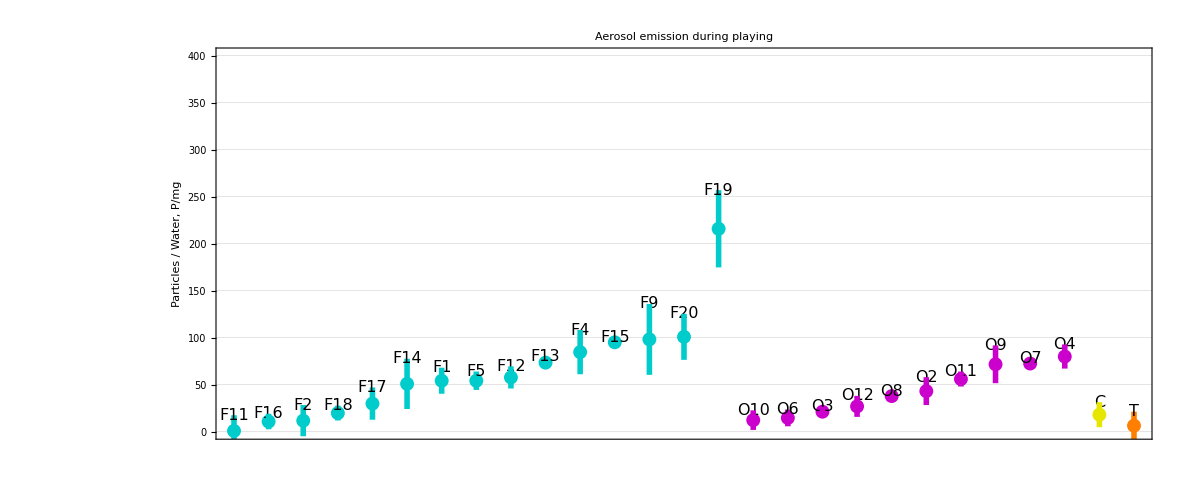

```mathematica
Clear[R,TaskPlotPerWater,
A,i]

R = {-100*0,400};

TaskPlotPerWater[task_?StringQ] := Module[{A,i},
A = SelectRows[Z,"Aufgabe"/.ToEnglish,(#==task)&];
If[Length[A]==2,Return[1]];
A = Drop[ExtractColumn[A,{"Instrument","Partikel/Wasser (P/mg)","ER σ (P/s)","Emissionsrate (P/s)","Proband"}/.ToEnglish],2];
A = Select[A,NumericQ[#[[2]]]&];
If[A=={},Return[2]];
A = Transpose[A];
A[[3]] *= A[[2]]/A[[4]];
A = Drop[A,{4}];
A = Transpose[A];
A = Transpose[MyPartition[1,A]];
A = Insert[A,
A[[1]]/.({
"Qu"->CMYKColor[1,0,0,0.2],
"Ob"->CMYKColor[0,1,0,0.2],
"KP"->CMYKColor[0,0,0,0.3],
"Kl"->CMYKColor[0,0,1,0.1],
"Tr"->CMYKColor[0,0.5,1,0]}/.ToEnglish),
2];
A[[1]] = A[[1]]/.({"Kl"->3,"KP"->5,"Ob"->2,"Qu"->1,"Tr"->4}/.ToEnglish);
A = Transpose[A];
A = Select[A,(#[[1]]≤4)&];
A = A/.{
"C2"->"C",
"T1"->"T"};
A = Rest/@SortBy[A,First];
A = Transpose[A];
i = 0;
A[[2]] = Map[
Flatten[
Map[(
++i;
{Point[{i,#[[1]]}],
Line[h={
{i,Max[-Infinity,#[[1]]-#[[2]]]},
{i,                                  #[[1]]+#[[2]]   }}],
Text@@Prepend[
If[MemberQ[{ (* "Playing" *) },task],
{h[[1]],{0,   2}},
{h[[2]],{0,-2}}],
Style[
StringDrop[#[[3]],0],
FontColor->GrayLevel[0],
FontFamily->"Arial",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->Round[(FontSize/.MyTS)*2/3]]]}
)&,SortBy[#,First]]
]&,A[[2]]];
A = Flatten/@Transpose[A];
A = Graphics[
{AbsoluteThickness[  4],
AbsolutePointSize[10],
A},
AspectRatio->0.4,
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{None,"Particles / Water,   P/mg"},
FrameTicks->{None,Automatic},
GridLines  ->{None,Automatic},
ImageSize->1200,
LabelStyle->MyTS,
PlotLabel->StringJoin["Aerosol emission during ",ToLowerCase[task]],
PlotRange->{All,R},
PlotRangeClipping->True];

Print[
MDExport[
StringJoin[OutPath,"TaskPlots\\P-mg\\",task,"_PerWater.tif"],
Rasterize[A],
"ImageEncoding"->"LZW"]];
A];


TaskPlotPerWater[{"Musikspiel","Musikspiel"}[[1]]/.ToEnglish]
```

```mathematica
TaskPlotPerWater/@Measurements;
```

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-mg\Breathing_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-mg\Speaking With Surgical Mask_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-mg\Speaking_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-mg\Playing With Surgical Mask_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-mg\Playing_PerWater.tif

Creating new directory  C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Ob~Musikspiel(Sprechen)_PerWater.tif

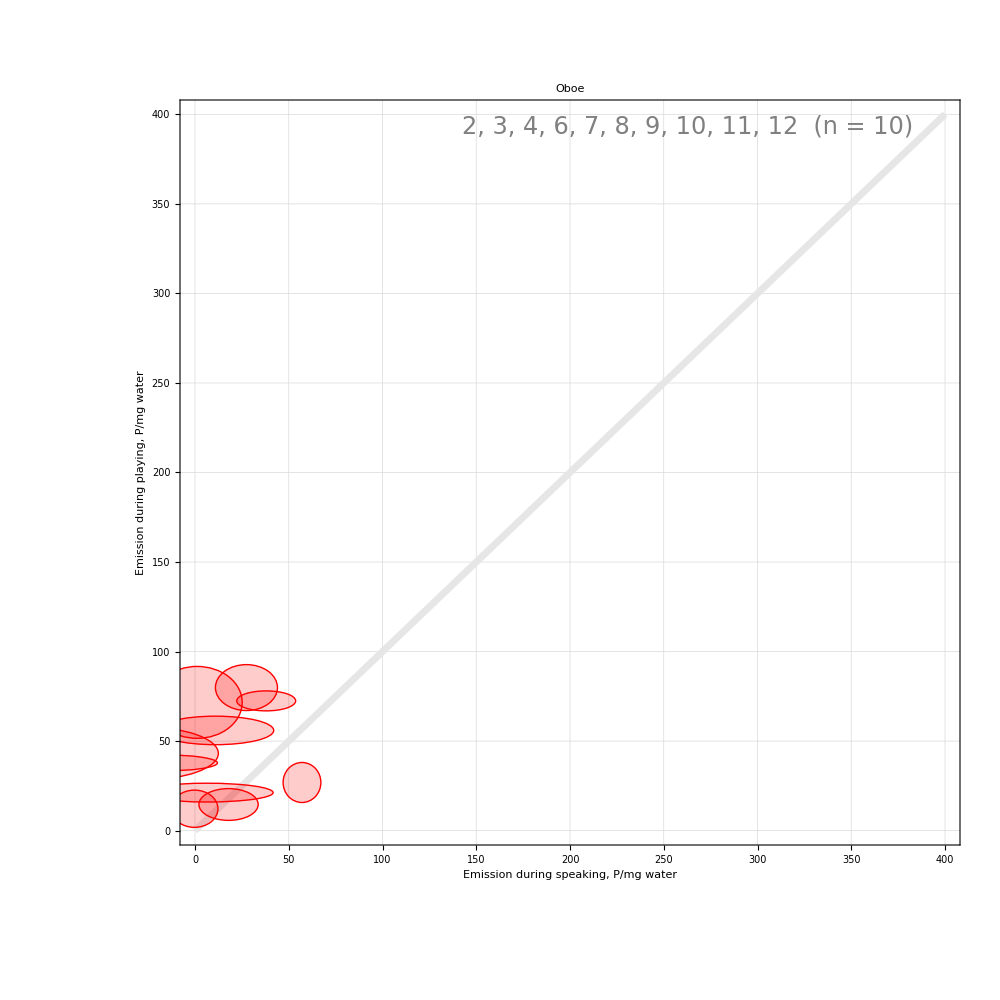

```mathematica
Clear[R,CorrPlotPerWater,
A,a,c,p]

R = {-100*0,400};

CorrPlotPerWater[
instr_?StringQ,
        X_?StringQ,
        Y_?StringQ] := Module[{A,a,c,p},
A = SelectRows[Z,"Instrument"/.ToEnglish,(#==(instr/.ToEnglish))&];
If[a=(Length[A]==2),A = Z];
A = {
SelectRows[A,"Aufgabe"/.ToEnglish,(#==(X/.ToEnglish))&],
SelectRows[A,"Aufgabe"/.ToEnglish,(#==(Y/.ToEnglish))&]};
If[Min[Length/@A]==2,Return[2]];
A = Map[Drop[ExtractColumn[#,{"Proband","Partikel/Wasser (P/mg)","ER σ (P/s)","Emissionsrate (P/s)"}/.ToEnglish],2]&,A];
A = Map[Select[#,NumericQ[#[[2]]]&]&,A];
If[Min[Length/@A]==0,Return[3]];
A = Map[{#[[1]],#[[2]],#[[2]]*#[[3]]/#[[4]]}&,A,{2}];
A = MyMerge[A[[1]],A[[2]],1,True];
If[A=={},Return[4]];
p = Map[StringDrop[#,1]&,First/@A];
p = SortBy[p,ToExpression];
p = ConcatStringList[p,", "];
p = StringJoin[p,"  (n = ",ToString[Length[A]],")"];
A = Last/@A;
A = Transpose/@A;
c = Y/.{
"Atmen"                                       ->Hue[2/3,0.6,1],
"Sprechen mit MNS"              ->Hue[1/3,0.4,0.9],
"Sprechen"                                ->Hue[1/3,1.0,0.8],
"Musikspiel mit Schutz"  ->Hue[0/3,0.4,1],
"Musikspiel"                           ->Hue[0/3,1.0,1],
"Luftreiniger"                       ->PatternFilling["Hexagon",ImageScaled[0.008]],
"Messbereich"                         ->GrayLevel[0.7],
"Proband im Messbereich"->GrayLevel[0.9],
"Ventilator"                           ->PatternFilling["Chevron",ImageScaled[0.005]]};

A = Graphics[
{If[True,
{AbsoluteThickness[5],GrayLevel[0.9],
If[ListQ[R],
Line[{{0,0},ConstantArray[Last[R],2]}],
If[NumericQ[R],
Line[{{0,0},ConstantArray[R,2]}],
Nothing]]},
Nothing],
Text[
Style[If[a,"",p],
FontColor->GrayLevel[0.5],
FontFamily->"Arial",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->24],
Scaled[{0.94,0.98}],
{1,1}],
AbsoluteThickness[1],
c                     ,Circle@@@A,
Opacity[0.2],Disk@@@A},
AspectRatio->If[R===All,1,Automatic],
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{
StringJoin["Emission during ",ToLowerCase[X/.ToEnglish],",   P/mg water"],
StringJoin["Emission during ",ToLowerCase[Y/.ToEnglish],",   P/mg water"]},
GridLines->Automatic,
ImageSize->1000,
LabelStyle->MyTS,
PlotLabel->instr/.{"Alle"->"All","Kl"->"Clarinet","KP"->"Singing","Ob"->"Oboe","Qu"->"Flute","Tr"->"Trumpet"},
PlotRange->{R,R},
PlotRangeClipping->True];

Print[
MDExport[
StringJoin[OutPath,"CorrPlots\\P-mg\\",instr,"~",Y,"(",X,")_PerWater.tif"],
Rasterize[A],
"ImageEncoding"->"LZW"]];
A];


CorrPlotPerWater["Ob","Sprechen","Musikspiel"]
```

```mathematica
Scan[(
CorrPlotPerWater[#,"Sprechen","Atmen"];
CorrPlotPerWater[#,"Sprechen","Sprechen mit MNS"];
CorrPlotPerWater[#,"Sprechen","Musikspiel"];
CorrPlotPerWater[#,"Atmen"       ,"Musikspiel"];
CorrPlotPerWater[#,"Musikspiel","Musikspiel mit Schutz"]
)&,
{"Alle","Qu","Ob","KP","Kl","Tr"}];
```

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Alle~Atmen(Sprechen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Alle~Sprechen mit MNS(Sprechen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Alle~Musikspiel(Sprechen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Alle~Musikspiel(Atmen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Alle~Musikspiel mit Schutz(Musikspiel)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Qu~Atmen(Sprechen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Qu~Sprechen mit MNS(Sprechen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Qu~Musikspiel(Sprechen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Qu~Musikspiel(Atmen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Ob~Atmen(Sprechen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Ob~Sprechen mit MNS(Sprechen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Ob~Musikspiel(Sprechen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Ob~Musikspiel(Atmen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Ob~Musikspiel mit Schutz(Musikspiel)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\KP~Atmen(Sprechen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\KP~Sprechen mit MNS(Sprechen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\KP~Musikspiel(Sprechen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\KP~Musikspiel(Atmen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Kl~Atmen(Sprechen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Kl~Musikspiel(Sprechen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Kl~Musikspiel(Atmen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Kl~Musikspiel mit Schutz(Musikspiel)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Tr~Musikspiel(Sprechen)_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Tr~Musikspiel mit Schutz(Musikspiel)_PerWater.tif

0.798748

0.798748

Creating new directory  C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Qu~Musikspiel(Sprechen)_Water.tif

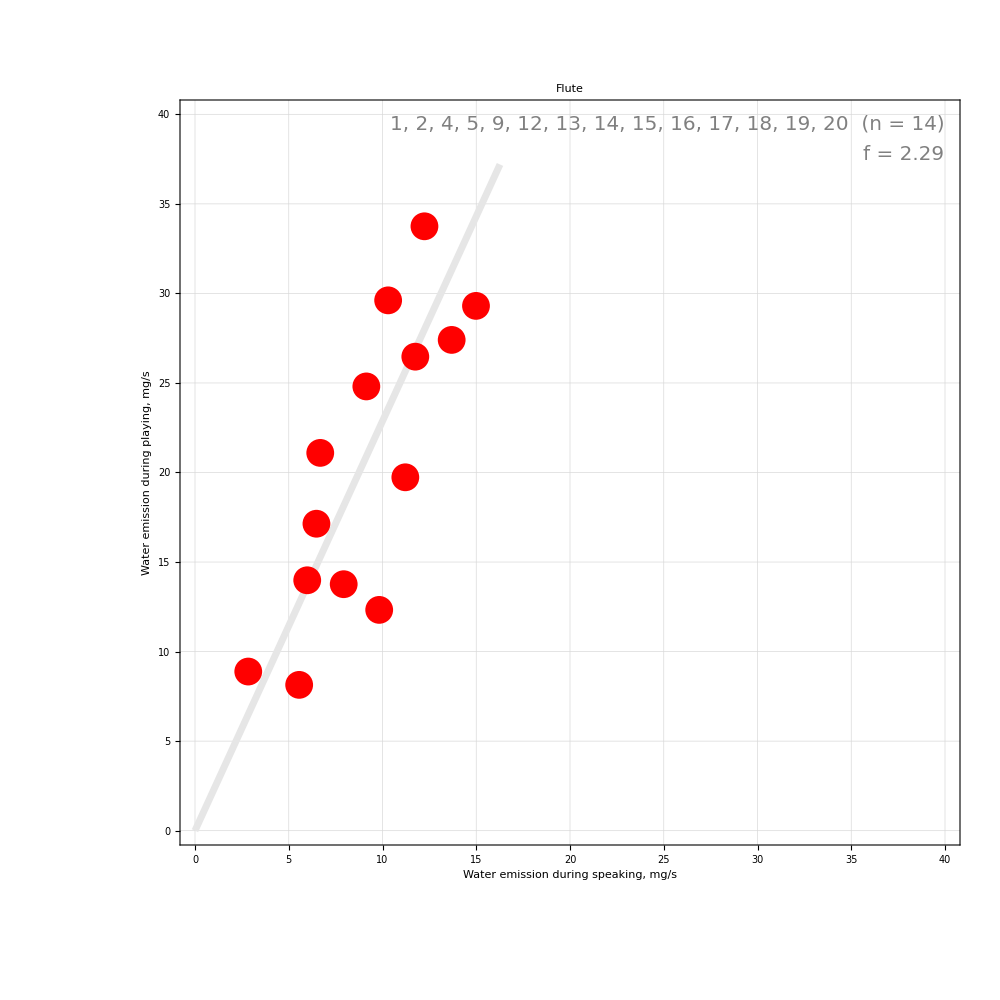

```mathematica
Clear[R,CorrPlotWater,
A,a,c,g,p,s,x,α]

R = 40;

CorrPlotWater[
instr_?StringQ,
        X_?StringQ,
        Y_?StringQ] := Module[{A,a,c,g,p,s,x,α},
A = SelectRows[Z,"Instrument"/.ToEnglish,(#==(instr/.ToEnglish))&];
If[a=(Length[A]==2),A = Z];
A = {
SelectRows[A,"Aufgabe"/.ToEnglish,(#==(X/.ToEnglish))&],
SelectRows[A,"Aufgabe"/.ToEnglish,(#==(Y/.ToEnglish))&]};
If[Min[Length/@A]==2,Return[2]];
A = Map[Drop[ExtractColumn[#,{"Proband","Wasseremission (mg/s)"}/.ToEnglish],2]&,A];
A = Map[Select[#,NumericQ[#[[2]]]&]&,A];
If[Min[Length/@A]==0,Return[3]];
A = MyMerge[A[[1]],A[[2]],1,True];
If[A=={},Return[4]];
p = Map[StringDrop[#,1]&,First/@A];
p = SortBy[p,ToExpression];
p = ConcatStringList[p,", "];
p = StringJoin[p,"  (n = ",ToString[Length[A]],")"];
A = Last/@A;
A = Transpose/@A;
A = Flatten[A,1];
g = Map[({Cos[α],Sin[α]}.#)&,A];
g = NMinimize[g.g,α];
g = α/.g[[2]];
g = Tan[g+π/2];

{x,y} = Transpose[A];
Print[Correlation[x,y]];
x -= Mean[x];
y -= Mean[y];
Print[(x.y)/Sqrt[x.x*y.y]];

A = Point[A];
c = Y/.{
"Atmen"                                       ->Hue[2/3,0.6,1],
"Sprechen mit MNS"              ->Hue[1/3,0.4,0.9],
"Sprechen"                                ->Hue[1/3,1.0,0.8],
"Musikspiel mit Schutz"  ->Hue[0/3,0.4,1],
"Musikspiel"                           ->Hue[0/3,1.0,1],
"Luftreiniger"                       ->PatternFilling["Hexagon",ImageScaled[0.008]],
"Messbereich"                         ->GrayLevel[0.7],
"Proband im Messbereich"->GrayLevel[0.9],
"Ventilator"                           ->PatternFilling["Chevron",ImageScaled[0.005]]};
s = {
FontColor->GrayLevel[0.5],
FontFamily->"Arial",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->Round[(FontSize/.MyTS)*5/6]};
A = Graphics[
{Text[Style@@Prepend[s,If[a,"",p]                                                        ],Scaled[  0.98*{1,1}],{1,1}],
Text[Style@@Prepend[s,StringJoin["f = ",RealForm[g,4,2]]],Scaled[{0.98,0.94} ],{1,1}],
If[NumericQ[R],
{AbsoluteThickness[5],
GrayLevel[0.9],
Line[Transpose[{#,g*#}]&[
{0,0.93*R*Min[1,1/g]}]]},
Nothing],
AbsolutePointSize[20],c,A},
AspectRatio->If[R===All,1,Automatic],
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{
StringJoin["Water emission during ",ToLowerCase[X/.ToEnglish],",   mg/s"],
StringJoin["Water emission during ",ToLowerCase[Y/.ToEnglish],",   mg/s"]},
GridLines->Automatic,
ImageSize->1000,
LabelStyle->MyTS,
PlotLabel->instr/.{"Alle"->"All","Kl"->"Clarinet","KP"->"Singing","Ob"->"Oboe","Qu"->"Flute","Tr"->"Trumpet"},
PlotRange->{{0,R},{0,R}},
PlotRangeClipping->True];

Print[
MDExport[
StringJoin[OutPath,"CorrPlots\\mg-s\\",instr,"~",Y,"(",X,")_Water.tif"],
Rasterize[A],
"ImageEncoding"->"LZW"]];
A];


CorrPlotWater["Qu","Sprechen","Musikspiel"]
```

```mathematica
Scan[(
CorrPlotWater[#,"Sprechen","Atmen"];
CorrPlotWater[#,"Sprechen","Sprechen mit MNS"];
CorrPlotWater[#,"Sprechen","Musikspiel"];
CorrPlotWater[#,"Atmen"       ,"Musikspiel"];
CorrPlotWater[#,"Musikspiel","Musikspiel mit Schutz"]
)&,
{"Alle","Qu","Ob","KP","Kl","Tr"}];
```

0.666113

0.666113

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Alle~Atmen(Sprechen)_Water.tif

0.0680885

0.0680885

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Alle~Sprechen mit MNS(Sprechen)_Water.tif

0.789288

0.789288

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Alle~Musikspiel(Sprechen)_Water.tif

0.425898

0.425898

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Alle~Musikspiel(Atmen)_Water.tif

0.195492

0.195492

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Alle~Musikspiel mit Schutz(Musikspiel)_Water.tif

0.899105

0.899105

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Qu~Atmen(Sprechen)_Water.tif

0.519267

0.519267

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Qu~Sprechen mit MNS(Sprechen)_Water.tif

0.798748

0.798748

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Qu~Musikspiel(Sprechen)_Water.tif

0.699616

0.699616

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Qu~Musikspiel(Atmen)_Water.tif

0.896135

0.896135

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Ob~Atmen(Sprechen)_Water.tif

0.894459

0.894459

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Ob~Sprechen mit MNS(Sprechen)_Water.tif

0.713072

0.713072

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Ob~Musikspiel(Sprechen)_Water.tif

0.835778

0.835778

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Ob~Musikspiel(Atmen)_Water.tif

0.179122

0.179122

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Ob~Musikspiel mit Schutz(Musikspiel)_Water.tif

0.422881

0.422881

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\KP~Atmen(Sprechen)_Water.tif

-0.0281585

-0.0281585

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\KP~Sprechen mit MNS(Sprechen)_Water.tif

1.

1.

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\KP~Musikspiel(Sprechen)_Water.tif

1.

1.

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\KP~Musikspiel(Atmen)_Water.tif

Correlation::shlen: The argument {8.70055} should have at least two elements.

Correlation[{8.70055},{6.35133}]

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Kl~Atmen(Sprechen)_Water.tif

Correlation::shlen: The argument {8.70055} should have at least two elements.

Correlation[{8.70055},{19.6555}]

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Kl~Musikspiel(Sprechen)_Water.tif

Correlation::shlen: The argument {6.35133} should have at least two elements.

General::stop: Further output of Correlation::shlen will be suppressed during this calculation.

Correlation[{6.35133},{19.6555}]

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Indeterminate

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Kl~Musikspiel(Atmen)_Water.tif

Correlation[{19.6555},{7.36465}]

Indeterminate

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Kl~Musikspiel mit Schutz(Musikspiel)_Water.tif

Correlation[{13.4608},{30.0835}]

Indeterminate

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Tr~Musikspiel(Sprechen)_Water.tif

Correlation[{30.0835},{9.06738}]

Indeterminate

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Tr~Musikspiel mit Schutz(Musikspiel)_Water.tif

Creating new directory  C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Ob~Musikspiel mit Schutz(Musikspiel).tif

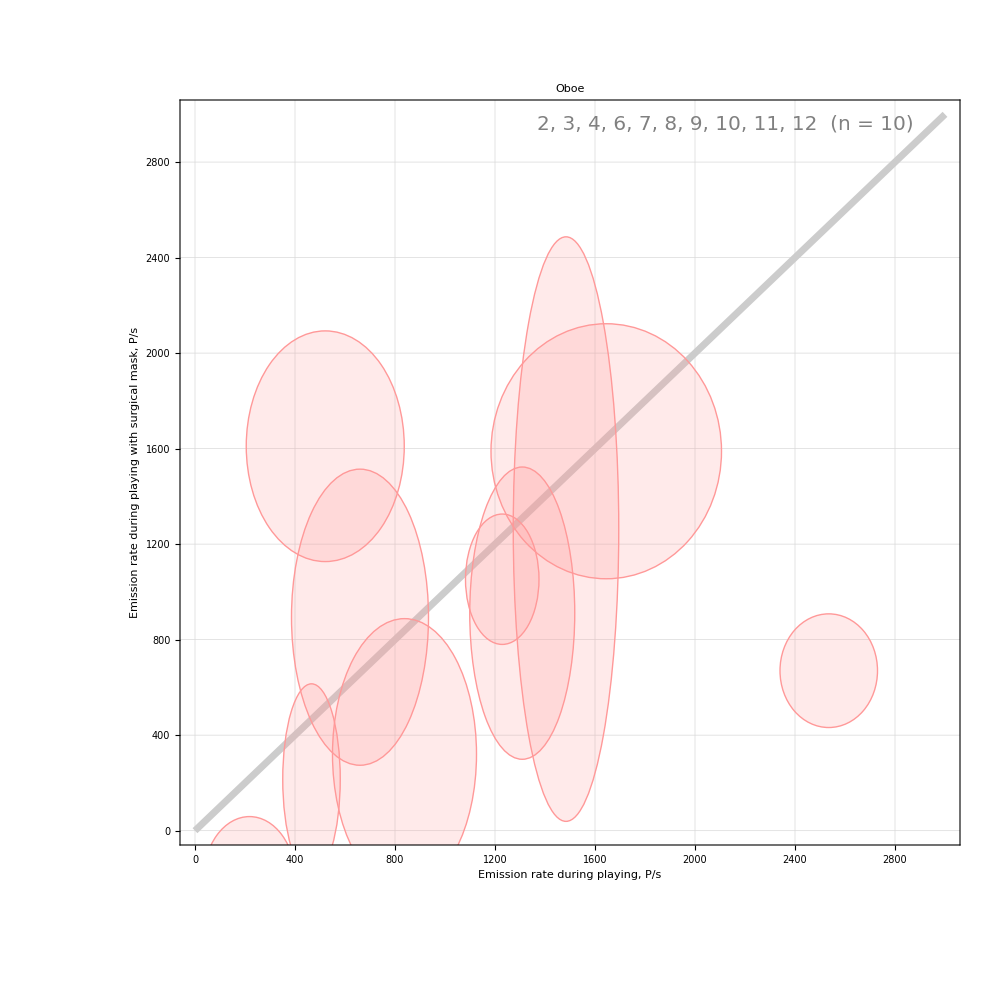

```mathematica
Clear[R,CorrPlot,
A,a,c,p]

R = {-600*0,3000};

CorrPlot[
instr_?StringQ,
        X_?StringQ,
        Y_?StringQ] := Module[{A,a,c,p},
A = SelectRows[Z,"Instrument"/.ToEnglish,(#==(instr/.ToEnglish))&];
If[a=(Length[A]==2),A = Z];
A = {
SelectRows[A,"Aufgabe"/.ToEnglish,(#==(X/.ToEnglish))&],
SelectRows[A,"Aufgabe"/.ToEnglish,(#==(Y/.ToEnglish))&]};
If[Min[Length/@A]==2,Return[2]];
A = Map[Drop[ExtractColumn[#,{"Proband","Emissionsrate (P/s)","ER σ (P/s)"}/.ToEnglish],2]&,A];
A = MyMerge[A[[1]],A[[2]],1,True];
If[A=={},Return[3]];
p = Map[StringDrop[#,1]&,First/@A];
p = SortBy[p,ToExpression];
p = ConcatStringList[p,", "];
p = StringJoin[p,"  (n = ",ToString[Length[A]],")"];
A = Last/@A;
A = Transpose/@A;
c = Y/.{
"Atmen"                                       ->Hue[2/3,0.6,1],
"Sprechen mit MNS"              ->Hue[1/3,0.4,0.9],
"Sprechen"                                ->Hue[1/3,1.0,0.8],
"Musikspiel mit Schutz"  ->Hue[0/3,0.4,1],
"Musikspiel"                           ->Hue[0/3,1.0,1],
"Luftreiniger"                       ->PatternFilling["Hexagon",ImageScaled[0.008]],
"Messbereich"                         ->GrayLevel[0.7],
"Proband im Messbereich"->GrayLevel[0.9],
"Ventilator"                           ->PatternFilling["Chevron",ImageScaled[0.005]]};
A = Graphics[
{If[True,
{AbsoluteThickness[5],GrayLevel[0.8],
If[ListQ[R],
Line[{{0,0},ConstantArray[Last[R],2]}],
If[NumericQ[R],
Line[{{0,0},ConstantArray[R,2]}],
Nothing]]},
Nothing],
Text[
Style[If[a,"",p],
FontColor->GrayLevel[0.5],
FontFamily->"Arial",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->Round[(FontSize/.MyTS)*5/6]],
Scaled[{0.94,0.98}],
{1,1}],
AbsoluteThickness[1],
c                     ,Circle@@@A,
Opacity[0.2],Disk@@@A},
AspectRatio->If[R===All,1,Automatic],
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{
StringJoin["Emission rate during ",ToLowerCase[X/.ToEnglish],",  P/s"],
StringJoin["Emission rate during ",ToLowerCase[Y/.ToEnglish],",  P/s"]},
GridLines->Automatic,
ImageSize->1000,
LabelStyle->MyTS,
PlotLabel->instr/.{"Alle"->"All","Kl"->"Clarinet","KP"->"Singing","Ob"->"Oboe","Qu"->"Flute","Tr"->"Trumpet"},
PlotRange->{R,R},
PlotRangeClipping->True];

Print[
MDExport[
StringJoin[OutPath,"CorrPlots\\P-s\\",instr,"~",Y,"(",X,").tif"],
Rasterize[A],
"ImageEncoding"->"LZW"]];
A];


CorrPlot["Ob","Musikspiel","Musikspiel mit Schutz"]
```

```mathematica
Scan[(
CorrPlot[#,"Sprechen","Atmen"];
CorrPlot[#,"Sprechen","Sprechen mit MNS"];
CorrPlot[#,"Sprechen","Musikspiel"];
CorrPlot[#,"Atmen"       ,"Musikspiel"];
CorrPlot[#,"Musikspiel","Musikspiel mit Schutz"]
)&,
{"Alle","Qu","Ob","KP","Kl","Tr"}];
```

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Alle~Atmen(Sprechen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Alle~Sprechen mit MNS(Sprechen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Alle~Musikspiel(Sprechen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Alle~Musikspiel(Atmen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Alle~Musikspiel mit Schutz(Musikspiel).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Qu~Atmen(Sprechen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Qu~Sprechen mit MNS(Sprechen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Qu~Musikspiel(Sprechen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Qu~Musikspiel(Atmen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Ob~Atmen(Sprechen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Ob~Sprechen mit MNS(Sprechen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Ob~Musikspiel(Sprechen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Ob~Musikspiel(Atmen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Ob~Musikspiel mit Schutz(Musikspiel).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\KP~Atmen(Sprechen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\KP~Sprechen mit MNS(Sprechen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\KP~Musikspiel(Sprechen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\KP~Musikspiel(Atmen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Kl~Atmen(Sprechen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Kl~Musikspiel(Sprechen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Kl~Musikspiel(Atmen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Kl~Musikspiel mit Schutz(Musikspiel).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Tr~Musikspiel(Sprechen).tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Tr~Musikspiel mit Schutz(Musikspiel).tif

```mathematica
M = Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/AllCounts.dat"]];
Length[M]
```

44

```mathematica
DeleteDuplicates[Join@@Map[First,M,{2}]]
```

{Proband,Übersicht,group,sex,day_date,birthday,age,height,weight,body_temp,beard,resp_dis,nic_abu,py,annot,task_order1,task_order2,task_order3,task_order4,task_order5,exper,gradu,work_dom_1,work_dom_2,work_dom_3,work_dom_4,work_dom_5,Atmen,Sprechen,Musikspiel mit Schutz,Musikspiel,vor dem Atmen,vor dem Sprechen,vor dem Musikspiel mit Schutz,vor dem Musikspiel,Messbereich,Ventilator,Aerosolspektrometer 50 cm,Aerosolspektrometer 150 cm,Aerosolspektrometer 300 cm,Anemometer,Luftreiniger,Tonaufnahme,Proband im Messbereich,Messzeitraum,Sprechen mit MNS,vor dem Sprechen mit MNS,Thermohygrometer}

```mathematica
h = {"Proband",
"age","sex","height","weight",
"beard","resp_dis","nic_abu",
"exper"};
```

```mathematica
M = h/.M;
M = M/.{
"keine"->"",
"no"->"",
"n.v."->""};
MatrixForm[M]
```

(Kl02 | 28. | m | 174. | 75. | full |  | abu | 20.
KP01 | 26. | f | 172. | 56. |  |  |  | 
KP02 | 27. | m | 181. | 64. | full |  |  | 
KP03 | 20. | d | 170. | 75. |  | Asthma bronchiale (aktuell nicht exazerbiert) |  | 
KP04 | 30. | f | 173. | 59. |  |  |  | 
KP05 | 30. | m | 180. | 75. |  |  |  | 
KP06 | 29. | f | 165. | 58. |  |  |  | 
KP07 | 27. | f | 163. | 51. |  |  |  | 
KP08 | 28. | f | 162. | 55. |  |  |  | 
KP09 | 30. | m | 169. | 68. | full |  |  | 
KP10 | 52. | m | 183. | 80. | 3d |  |  | 
KP11 | 66. | m | 183. | 70. | full | allergisches Asthma (saisonal) |  | 
KP12 | 26. | m | 173. | 84. | 3d |  |  | 
Ob02 | 63. | f | 156. | 55. |  |  |  | 50.
Ob03 | 56. | f | 170. | 76. |  |  | s.p. | 44.
Ob04 | 53. | f | 183. | 72. |  |  |  | 40.
Ob05 | 54. | f | 171. | 70. |  |  | s.p. | 43.
Ob06 | 45. | m | 185. | 90. | 3d |  |  | 34.
Ob07 | 64. | m | 187. | 82. |  |  |  | 40.
Ob08 | 53. | m | 203. | 92. | 3d |  |  | 40.
Ob09 | 24. | f | 160. | 58. |  |  |  | 14.
Ob10 | 45. | m | 186. | 85. | 3d |  | abu | 30.
Ob11 | 65. | m | 176. | 63. |  |  |  | 55.
Ob12 | 42. | m | 189. | 90. |  |  | abu | 30.
Qu01 | 63. | m | 186. | 88. |  |  | abu | 50.
Qu02 | 47. | f | 161. | 74. |  |  |  | 35.
Qu03 | 47. | f | 158. | 72. |  |  |  | 38.
Qu04 | 68. | f | 158. | 95. |  |  |  | 58.
Qu05 | 63. | f | 172. | 55. |  |  |  | 53.
Qu06 | 26. | f | 166. | 75. |  |  |  | 15.
Qu07 | 50. | f | 156. | 54. |  |  |  | 39.
Qu09 | 64. | f | 164. | 65. |  |  |  | 50.
Qu10 | 26. | f | 168. | 65. |  |  | s.p. | 20.
Qu11 | 29. | f | 165. | 57. |  |  |  | 16.
Qu12 | 33. | f | 178. | 80. |  |  |  | 28.
Qu13 | 52. | f | 167. | 60. |  | allergisches Asthma |  | 40.
Qu14 | 38. | f | 165. | 66. |  |  |  | 27.
Qu15 | 59. | f | 163. | 55. |  |  |  | 40.
Qu16 | 37. | m | 180. | 76. | 3d |  |  | 27.
Qu17 | 23. | f | 173. | 56. |  |  |  | 11.
Qu18 | 56. | m | 180. | 80. |  |  |  | 45.
Qu19 | 64. | f | 167. | 50. |  |  |  | 50.
Qu20 | 46. | f | 168. | 61. |  |  |  | 35.
Tr01 | 26. | m | 182. | 90. | full |  |  | )

```mathematica
TableForm[
X = Prepend[M,h]]
```

Proband | age | sex | height | weight | beard | resp_dis | nic_abu | exper
Kl02 | 28. | m | 174. | 75. | full |  | abu | 20.
KP01 | 26. | f | 172. | 56. |  |  |  | 
KP02 | 27. | m | 181. | 64. | full |  |  | 
KP03 | 20. | d | 170. | 75. |  | Asthma bronchiale (aktuell nicht exazerbiert) |  | 
KP04 | 30. | f | 173. | 59. |  |  |  | 
KP05 | 30. | m | 180. | 75. |  |  |  | 
KP06 | 29. | f | 165. | 58. |  |  |  | 
KP07 | 27. | f | 163. | 51. |  |  |  | 
KP08 | 28. | f | 162. | 55. |  |  |  | 
KP09 | 30. | m | 169. | 68. | full |  |  | 
KP10 | 52. | m | 183. | 80. | 3d |  |  | 
KP11 | 66. | m | 183. | 70. | full | allergisches Asthma (saisonal) |  | 
KP12 | 26. | m | 173. | 84. | 3d |  |  | 
Ob02 | 63. | f | 156. | 55. |  |  |  | 50.
Ob03 | 56. | f | 170. | 76. |  |  | s.p. | 44.
Ob04 | 53. | f | 183. | 72. |  |  |  | 40.
Ob05 | 54. | f | 171. | 70. |  |  | s.p. | 43.
Ob06 | 45. | m | 185. | 90. | 3d |  |  | 34.
Ob07 | 64. | m | 187. | 82. |  |  |  | 40.
Ob08 | 53. | m | 203. | 92. | 3d |  |  | 40.
Ob09 | 24. | f | 160. | 58. |  |  |  | 14.
Ob10 | 45. | m | 186. | 85. | 3d |  | abu | 30.
Ob11 | 65. | m | 176. | 63. |  |  |  | 55.
Ob12 | 42. | m | 189. | 90. |  |  | abu | 30.
Qu01 | 63. | m | 186. | 88. |  |  | abu | 50.
Qu02 | 47. | f | 161. | 74. |  |  |  | 35.
Qu03 | 47. | f | 158. | 72. |  |  |  | 38.
Qu04 | 68. | f | 158. | 95. |  |  |  | 58.
Qu05 | 63. | f | 172. | 55. |  |  |  | 53.
Qu06 | 26. | f | 166. | 75. |  |  |  | 15.
Qu07 | 50. | f | 156. | 54. |  |  |  | 39.
Qu09 | 64. | f | 164. | 65. |  |  |  | 50.
Qu10 | 26. | f | 168. | 65. |  |  | s.p. | 20.
Qu11 | 29. | f | 165. | 57. |  |  |  | 16.
Qu12 | 33. | f | 178. | 80. |  |  |  | 28.
Qu13 | 52. | f | 167. | 60. |  | allergisches Asthma |  | 40.
Qu14 | 38. | f | 165. | 66. |  |  |  | 27.
Qu15 | 59. | f | 163. | 55. |  |  |  | 40.
Qu16 | 37. | m | 180. | 76. | 3d |  |  | 27.
Qu17 | 23. | f | 173. | 56. |  |  |  | 11.
Qu18 | 56. | m | 180. | 80. |  |  |  | 45.
Qu19 | 64. | f | 167. | 50. |  |  |  | 50.
Qu20 | 46. | f | 168. | 61. |  |  |  | 35.
Tr01 | 26. | m | 182. | 90. | full |  |  |

```mathematica
Column[
M = Map[((First[#]/.ToEnglish)->Rule@@@Transpose[Rest/@{h,#}])&,M]]
```

C2→{age→28.,sex→m,height→174.,weight→75.,beard→full,resp_dis→,nic_abu→abu,exper→20.}
S1→{age→26.,sex→f,height→172.,weight→56.,beard→,resp_dis→,nic_abu→,exper→}
S2→{age→27.,sex→m,height→181.,weight→64.,beard→full,resp_dis→,nic_abu→,exper→}
S3→{age→20.,sex→d,height→170.,weight→75.,beard→,resp_dis→Asthma bronchiale (aktuell nicht exazerbiert),nic_abu→,exper→}
S4→{age→30.,sex→f,height→173.,weight→59.,beard→,resp_dis→,nic_abu→,exper→}
S5→{age→30.,sex→m,height→180.,weight→75.,beard→,resp_dis→,nic_abu→,exper→}
S6→{age→29.,sex→f,height→165.,weight→58.,beard→,resp_dis→,nic_abu→,exper→}
S7→{age→27.,sex→f,height→163.,weight→51.,beard→,resp_dis→,nic_abu→,exper→}
S8→{age→28.,sex→f,height→162.,weight→55.,beard→,resp_dis→,nic_abu→,exper→}
S9→{age→30.,sex→m,height→169.,weight→68.,beard→full,resp_dis→,nic_abu→,exper→}
S10→{age→52.,sex→m,height→183.,weight→80.,beard→3d,resp_dis→,nic_abu→,exper→}
S11→{age→66.,sex→m,height→183.,weight→70.,beard→full,resp_dis→allergisches Asthma (saisonal),nic_abu→,exper→}
S12→{age→26.,sex→m,height→173.,weight→84.,beard→3d,resp_dis→,nic_abu→,exper→}
O2→{age→63.,sex→f,height→156.,weight→55.,beard→,resp_dis→,nic_abu→,exper→50.}
O3→{age→56.,sex→f,height→170.,weight→76.,beard→,resp_dis→,nic_abu→s.p.,exper→44.}
O4→{age→53.,sex→f,height→183.,weight→72.,beard→,resp_dis→,nic_abu→,exper→40.}
O5→{age→54.,sex→f,height→171.,weight→70.,beard→,resp_dis→,nic_abu→s.p.,exper→43.}
O6→{age→45.,sex→m,height→185.,weight→90.,beard→3d,resp_dis→,nic_abu→,exper→34.}
O7→{age→64.,sex→m,height→187.,weight→82.,beard→,resp_dis→,nic_abu→,exper→40.}
O8→{age→53.,sex→m,height→203.,weight→92.,beard→3d,resp_dis→,nic_abu→,exper→40.}
O9→{age→24.,sex→f,height→160.,weight→58.,beard→,resp_dis→,nic_abu→,exper→14.}
O10→{age→45.,sex→m,height→186.,weight→85.,beard→3d,resp_dis→,nic_abu→abu,exper→30.}
O11→{age→65.,sex→m,height→176.,weight→63.,beard→,resp_dis→,nic_abu→,exper→55.}
O12→{age→42.,sex→m,height→189.,weight→90.,beard→,resp_dis→,nic_abu→abu,exper→30.}
F1→{age→63.,sex→m,height→186.,weight→88.,beard→,resp_dis→,nic_abu→abu,exper→50.}
F2→{age→47.,sex→f,height→161.,weight→74.,beard→,resp_dis→,nic_abu→,exper→35.}
F3→{age→47.,sex→f,height→158.,weight→72.,beard→,resp_dis→,nic_abu→,exper→38.}
F4→{age→68.,sex→f,height→158.,weight→95.,beard→,resp_dis→,nic_abu→,exper→58.}
F5→{age→63.,sex→f,height→172.,weight→55.,beard→,resp_dis→,nic_abu→,exper→53.}
F6→{age→26.,sex→f,height→166.,weight→75.,beard→,resp_dis→,nic_abu→,exper→15.}
F7→{age→50.,sex→f,height→156.,weight→54.,beard→,resp_dis→,nic_abu→,exper→39.}
F9→{age→64.,sex→f,height→164.,weight→65.,beard→,resp_dis→,nic_abu→,exper→50.}
F10→{age→26.,sex→f,height→168.,weight→65.,beard→,resp_dis→,nic_abu→s.p.,exper→20.}
F11→{age→29.,sex→f,height→165.,weight→57.,beard→,resp_dis→,nic_abu→,exper→16.}
F12→{age→33.,sex→f,height→178.,weight→80.,beard→,resp_dis→,nic_abu→,exper→28.}
F13→{age→52.,sex→f,height→167.,weight→60.,beard→,resp_dis→allergisches Asthma,nic_abu→,exper→40.}
F14→{age→38.,sex→f,height→165.,weight→66.,beard→,resp_dis→,nic_abu→,exper→27.}
F15→{age→59.,sex→f,height→163.,weight→55.,beard→,resp_dis→,nic_abu→,exper→40.}
F16→{age→37.,sex→m,height→180.,weight→76.,beard→3d,resp_dis→,nic_abu→,exper→27.}
F17→{age→23.,sex→f,height→173.,weight→56.,beard→,resp_dis→,nic_abu→,exper→11.}
F18→{age→56.,sex→m,height→180.,weight→80.,beard→,resp_dis→,nic_abu→,exper→45.}
F19→{age→64.,sex→f,height→167.,weight→50.,beard→,resp_dis→,nic_abu→,exper→50.}
F20→{age→46.,sex→f,height→168.,weight→61.,beard→,resp_dis→,nic_abu→,exper→35.}
T1→{age→26.,sex→m,height→182.,weight→90.,beard→full,resp_dis→,nic_abu→,exper→}

```mathematica
Clear[h,t]
t = "Atmen"/.ToEnglish;
h = SelectRows[Z,"Aufgabe"/.ToEnglish,(#==t)&];
h = ExtractColumn[h,{"Proband","Wasseremission (mg/s)"}/.ToEnglish];
h = Transpose[Select[Drop[h,2],NumericQ[#[[2]]]&]];
h[[1]] = h[[1]]/.M;
h = {
"weight"/.h[[1]],
"height"/.h[[1]],
h[[2]]};
```

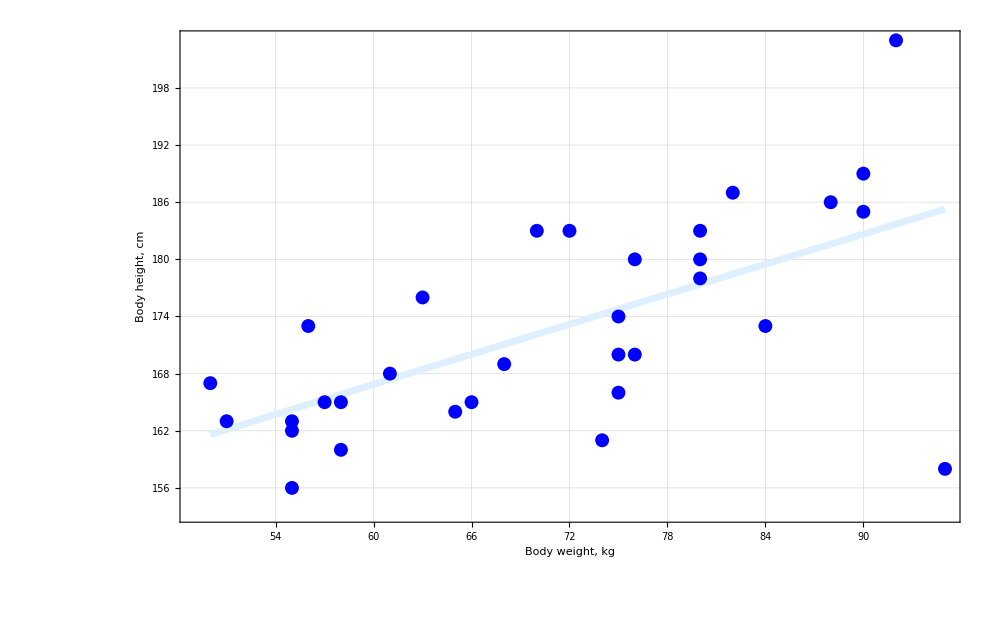

```mathematica
ListPlot[g=Transpose[h[[{
1,2
}]]],
AspectRatio->0.618,
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{"Body weight,  kg","Body height,  cm"},
GridLines->Automatic,
ImageSize->(i=1000),
LabelStyle->MyTS,
PlotRange->All,
PlotStyle->{{PointSize[0.01],Blue}},
Prolog->(
g = {MinMax[First/@g],Evaluate[Fit[g,{1,#},#]]&};
g[[2]] = g[[2]]/@g[[1]];
g = Line[Transpose[g]];
{AbsoluteThickness[5],LightBlue,g})]
```

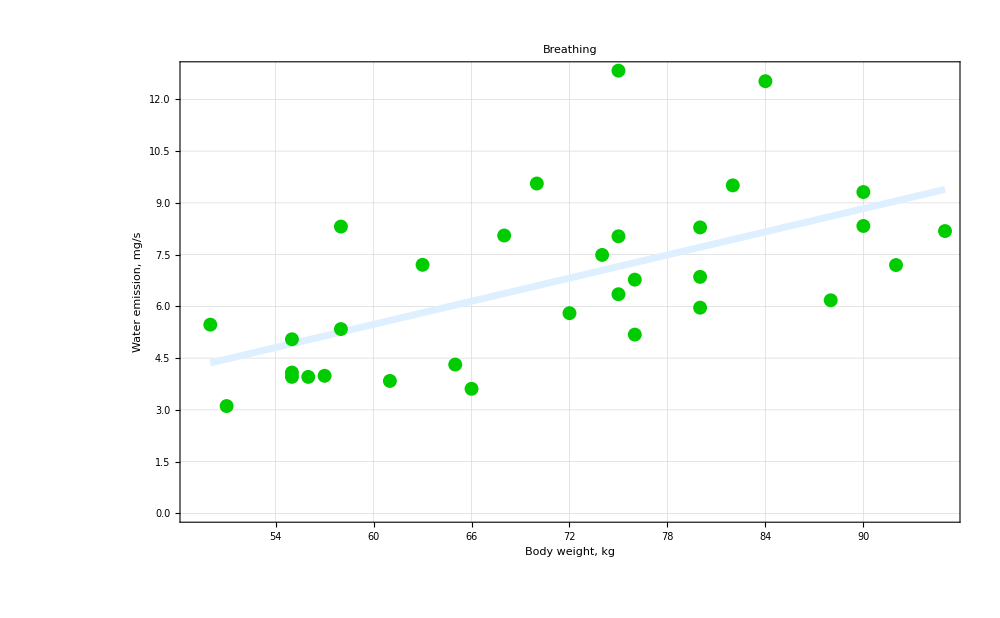

```mathematica
ListPlot[g=Transpose[h[[{
1,3
}]]],
AspectRatio->0.618,
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{"Body weight,  kg","Water emission,  mg/s"},
GridLines->Automatic,
ImageSize->(i=1000),
LabelStyle->MyTS,
PlotLabel->t,
PlotRange->All,
PlotStyle->{{PointSize[0.01],RGBColor[0,0.8,0]}},
Prolog->(
g = {MinMax[First/@g],Evaluate[Fit[g,{1,#},#]]&};
g[[2]] = g[[2]]/@g[[1]];
g = Line[Transpose[g]];
{AbsoluteThickness[5],LightBlue,g})]
```

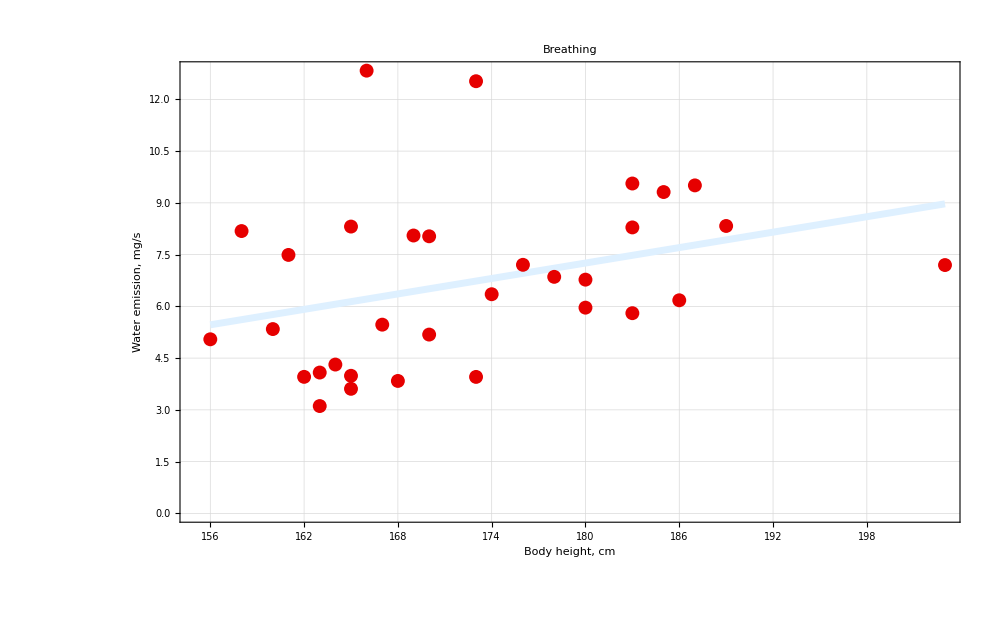

```mathematica
ListPlot[g=Transpose[h[[{
2,3
}]]],
AspectRatio->0.618,
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{"Body height,  cm","Water emission,  mg/s"},
GridLines->Automatic,
ImageSize->(i=1000),
LabelStyle->MyTS,
PlotLabel->t,
PlotRange->All,
PlotStyle->{{PointSize[0.01],RGBColor[0.9,0,0]}},
Prolog->(
g = {MinMax[First/@g],Evaluate[Fit[g,{1,#},#]]&};
g[[2]] = g[[2]]/@g[[1]];
g = Line[Transpose[g]];
{AbsoluteThickness[5],LightBlue,g})]
```

```mathematica
Column[Measurements]
```

Breathing
Speaking With Surgical Mask
Speaking
Playing With Surgical Mask
Playing

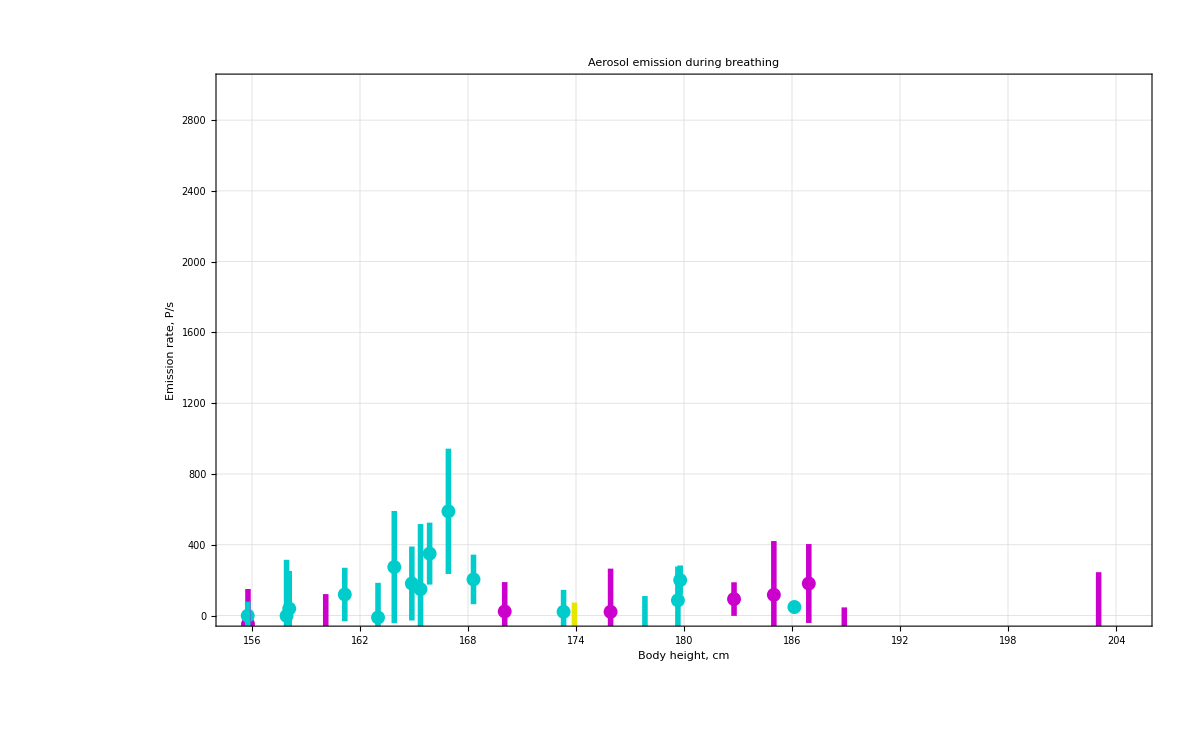

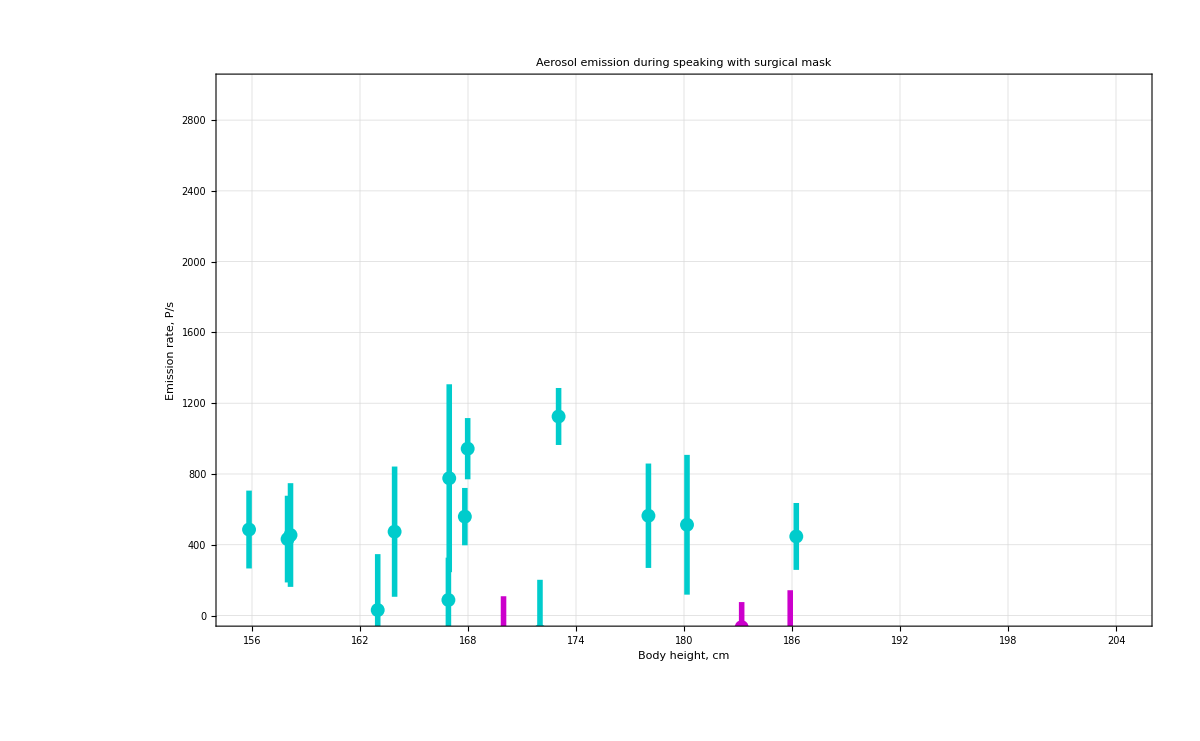

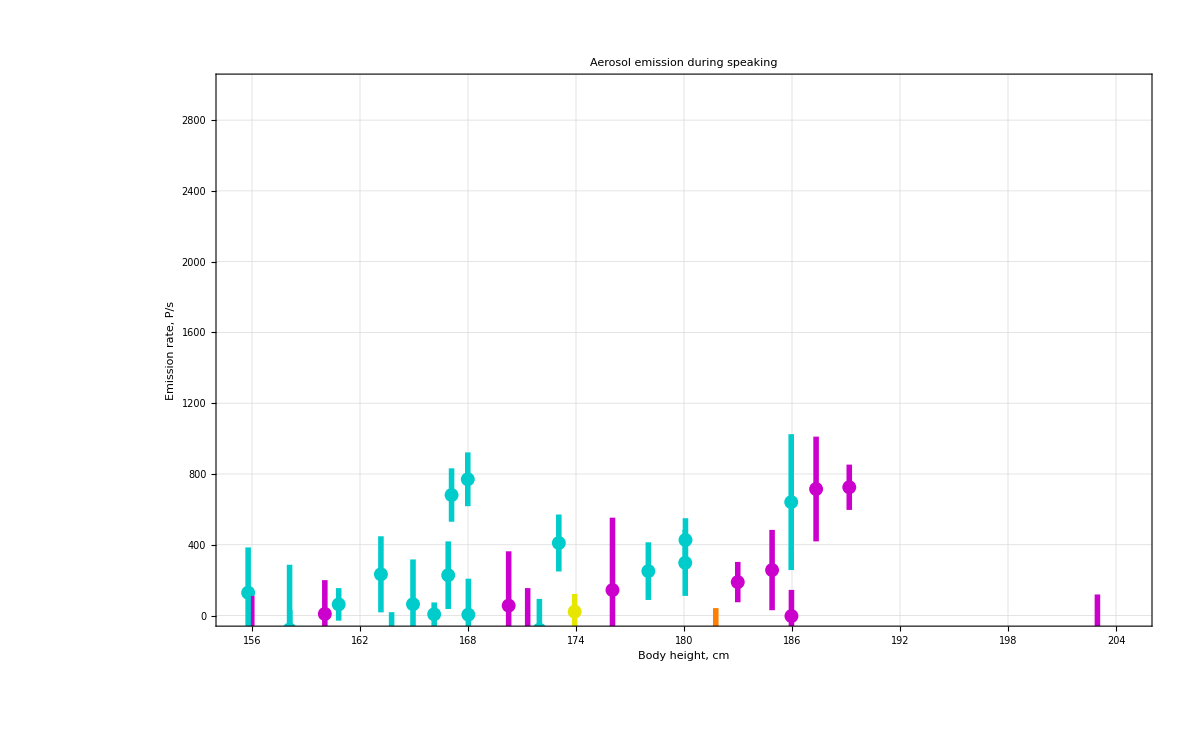

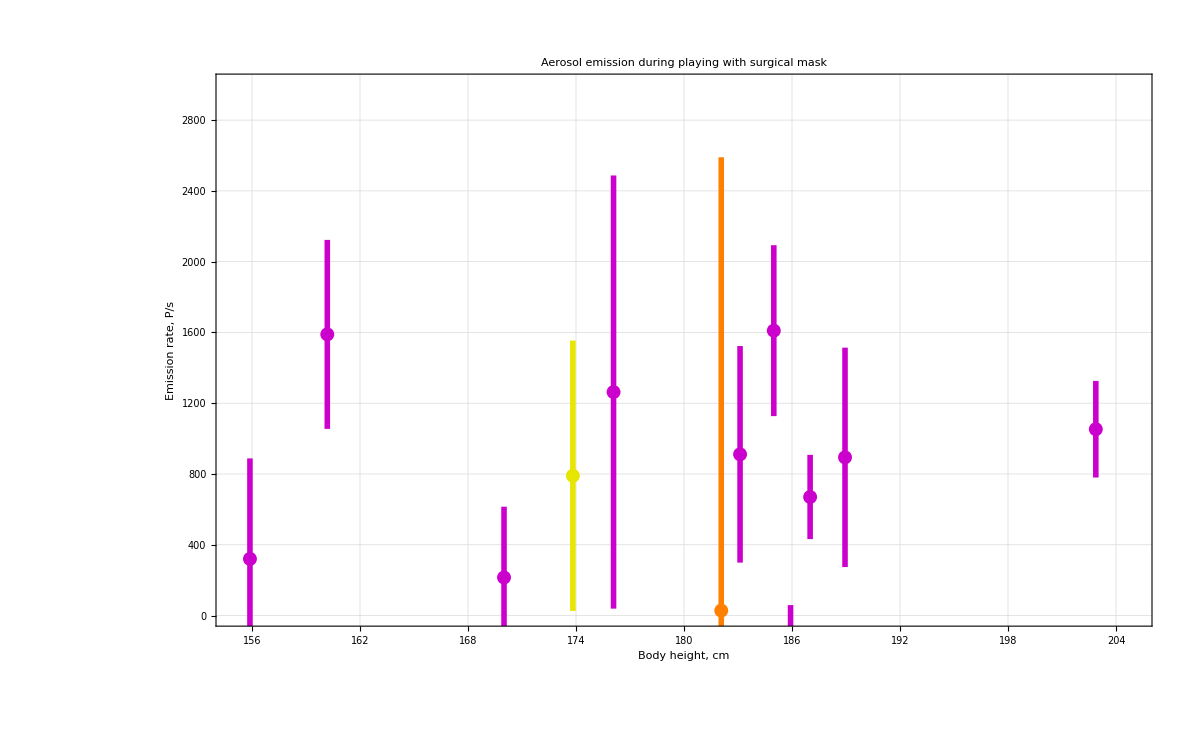

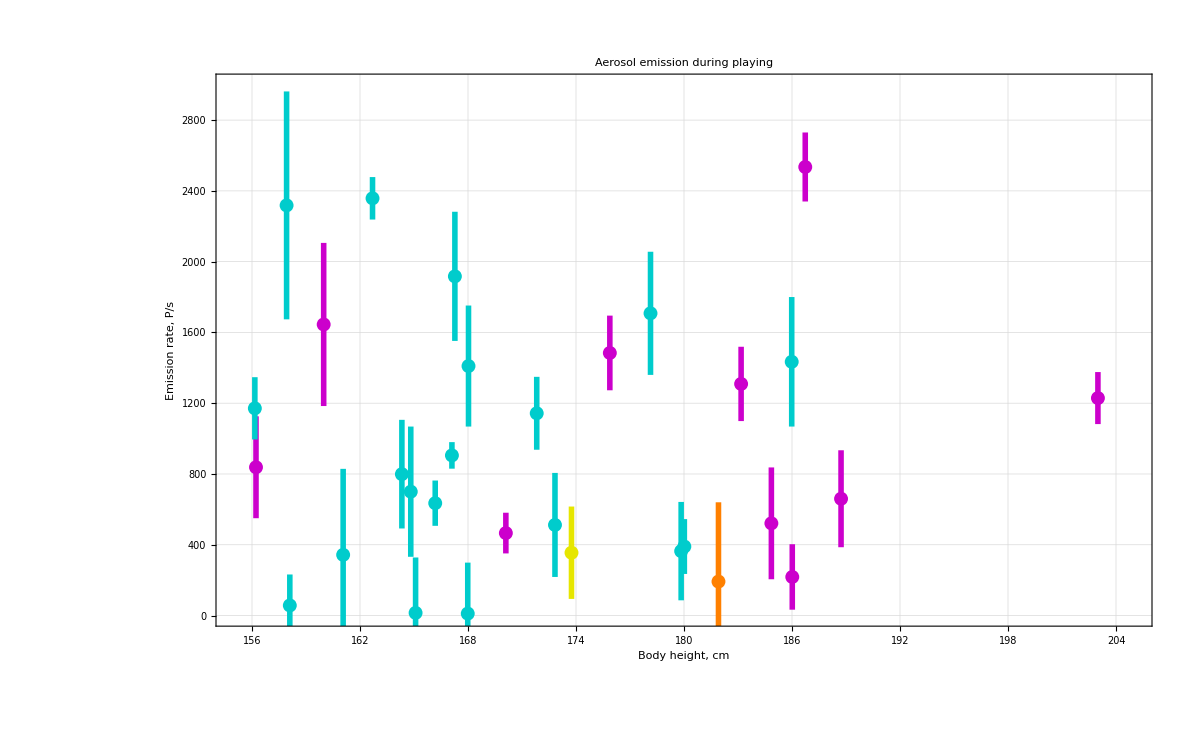

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Breathing_Emissionsrate (P-s)_height.tif
C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Speaking With Surgical Mask_Emissionsrate (P-s)_height.tif
C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Speaking_Emissionsrate (P-s)_height.tif
C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Playing With Surgical Mask_Emissionsrate (P-s)_height.tif
C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Playing_Emissionsrate (P-s)_height.tif

```mathematica
Column[
Map[(
Clear[G,h,t,x,y];
t = #;
G = SelectRows[Z,"Instrument",(#≠"S")&];
G = SelectRows[G,"Task",(#==t)&];
G = Drop[ExtractColumn[G,{y="Emissionsrate (P/s)","ER σ (P/s)","Proband","Instrument"}/.ToEnglish],2];
G = Transpose[G];
G[[3]] = G[[3]]/.(Rule@@@(Rest[ExtractColumn[X,{"Proband",x="height"}]]/.ToEnglish));
G[[4]] = G[[4]]/.({
"Qu"->CMYKColor[1,0,0,0.2],
"Ob"->CMYKColor[0,1,0,0.2],
"KP"->CMYKColor[0,0,0,0.3],
"Kl"->CMYKColor[0,0,1,0.1],
"Tr"->CMYKColor[0,0.5,1,0]}/.ToEnglish);
G = Transpose[G];
G = Map[{
#[[4]],
Point[{h=#[[3]]+RandomVariate[NormalDistribution[0,0.15]],#[[1]]}],
Line[{
{h,Max[-Infinity,#[[1]]-#[[2]]]},
{h,                                  #[[1]]+#[[2]]  }}]
}&,G];
Print[
G = Graphics[
{AbsoluteThickness[  4],
AbsolutePointSize[10],
G},
AspectRatio->0.618,
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{"Body height,  cm","Emission rate,  P/s"},
GridLines  ->Automatic,
ImageSize->1200,
LabelStyle->MyTS,
PlotLabel->StringJoin["Aerosol emission during ",ToLowerCase[t]],
PlotRange->{{155,205},{-300*0,3000}},
PlotRangeClipping->True]];
Export[
StringReplace[
StringJoin[OutPath,ConcatStringList[{t,y,x},"_"],".tif"],
{"/"->"-"}],
G])&,
Measurements]]
```

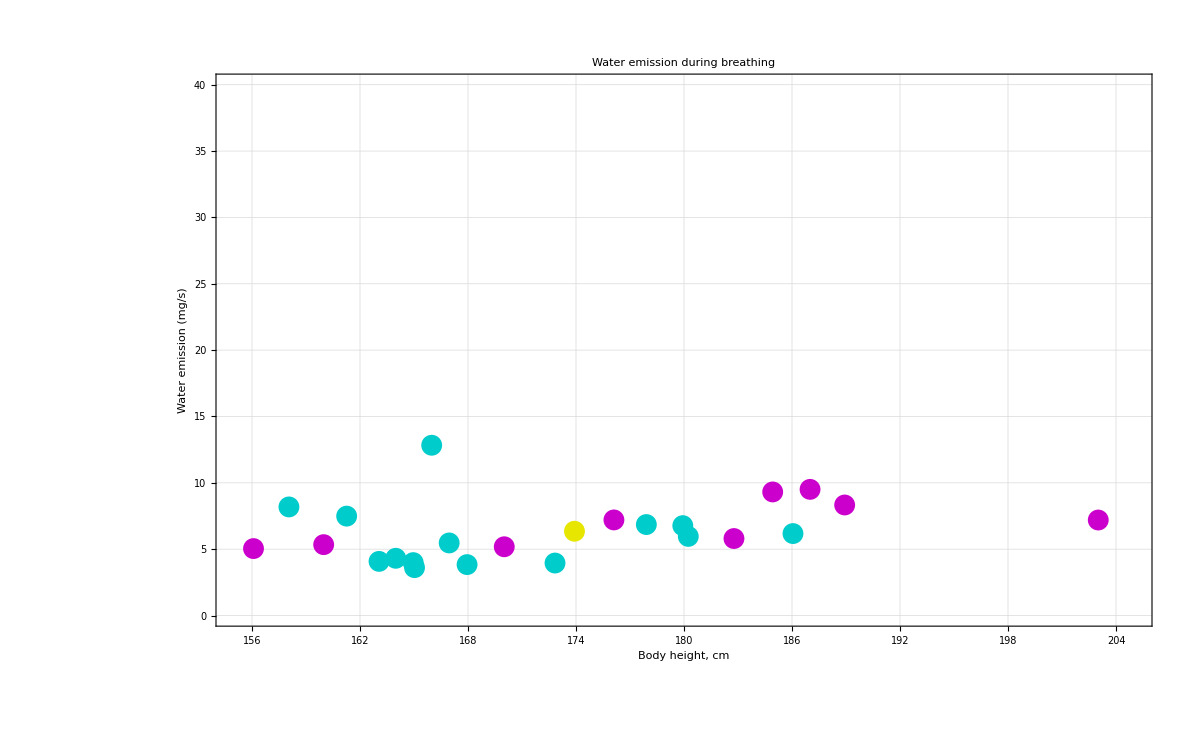

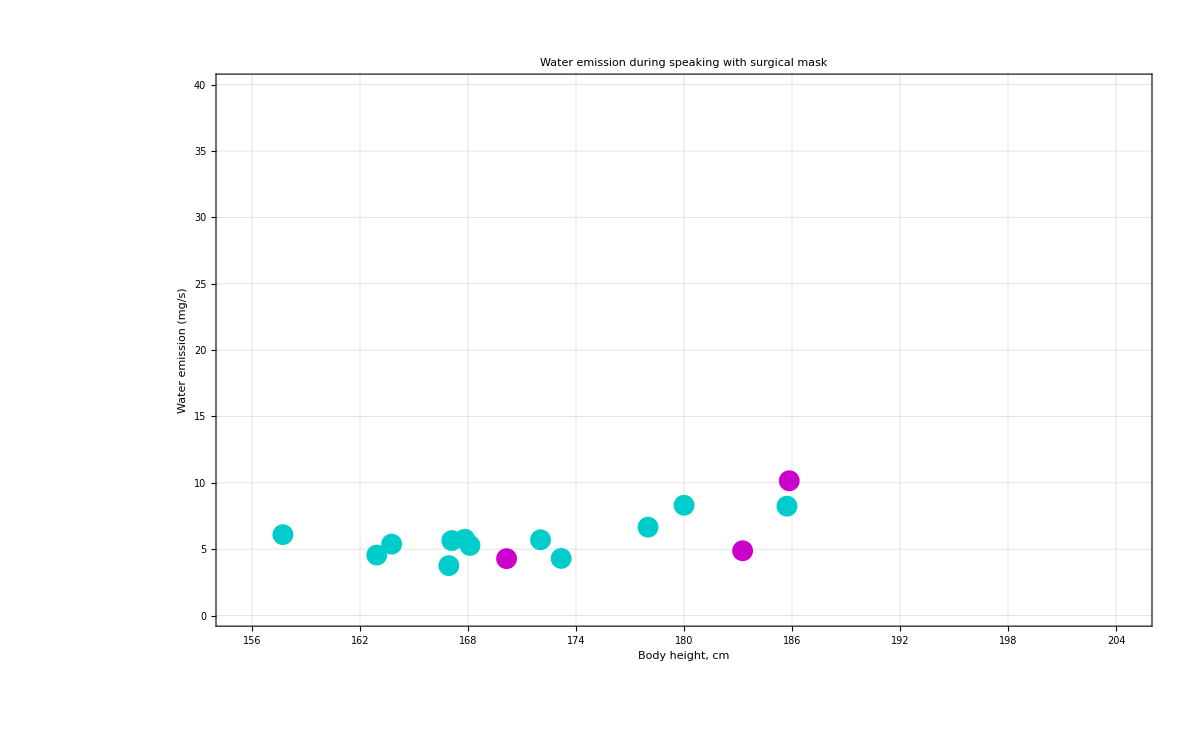

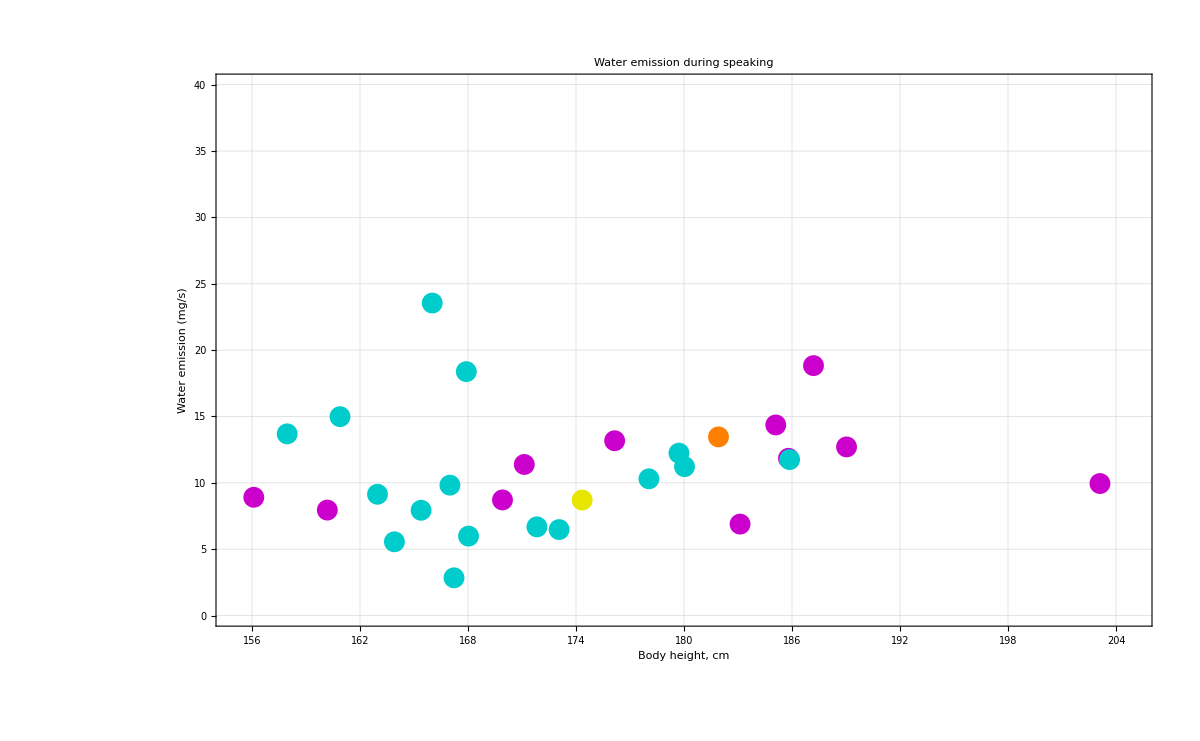

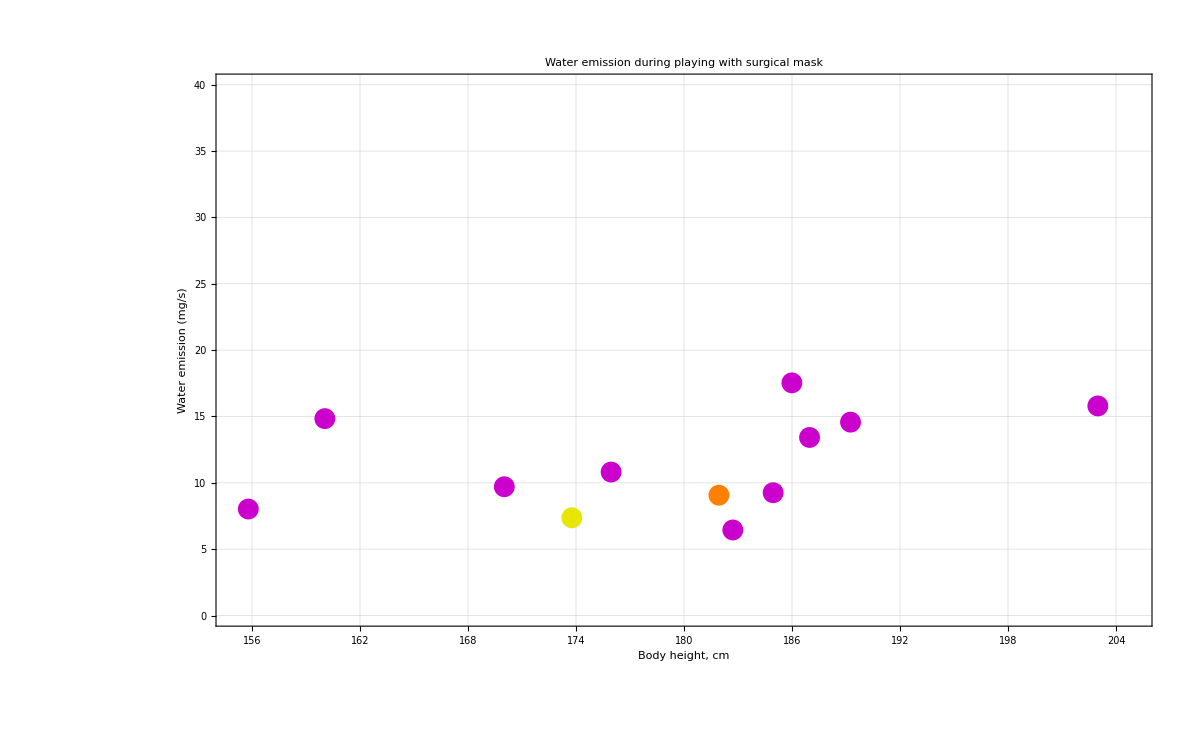

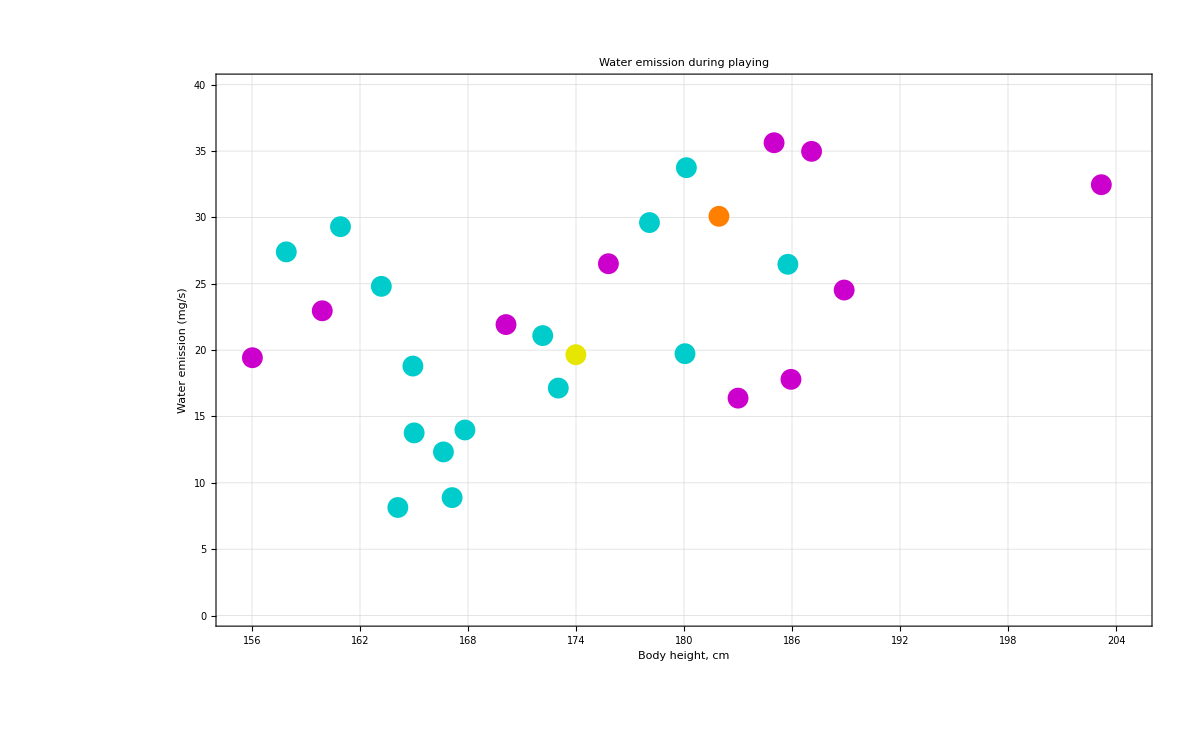

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Breathing_Water emission (mg-s)_height.tif
C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Speaking With Surgical Mask_Water emission (mg-s)_height.tif
C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Speaking_Water emission (mg-s)_height.tif
C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Playing With Surgical Mask_Water emission (mg-s)_height.tif
C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Playing_Water emission (mg-s)_height.tif

```mathematica
Column[
Map[(
Clear[G,h,t,x,y];
t = #;
G = SelectRows[Z,"Instrument",(#≠"S")&];
G = SelectRows[G,"Task",(#==t)&];
G = Drop[ExtractColumn[G,{y="Water emission (mg/s)","Proband","Instrument"}],2];
G = Select[G,NumericQ[#[[1]]]&];
G = Transpose[G];
G[[2]] = G[[2]]/.(Rule@@@(Rest[ExtractColumn[X,{"Proband",x="height"}]]/.ToEnglish));
G[[3]] = G[[3]]/.({
"Qu"->CMYKColor[1,0,0,0.2],
"Ob"->CMYKColor[0,1,0,0.2],
"KP"->CMYKColor[0,0,0,0.3],
"Kl"->CMYKColor[0,0,1,0.1],
"Tr"->CMYKColor[0,0.5,1,0]}/.ToEnglish);
G = Transpose[G];
G = Map[{
#[[3]],
Point[{h=#[[2]]+RandomVariate[NormalDistribution[0,0.15]],#[[1]]}]
}&,G];
Print[
G = Graphics[
{AbsolutePointSize[15],G},
AspectRatio->0.618,
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{"Body height,  cm",y},
GridLines  ->Automatic,
ImageSize->1200,
LabelStyle->MyTS,
PlotLabel->StringJoin["Water emission during ",ToLowerCase[t]],
PlotRange->{{155,205},{0,40}},
PlotRangeClipping->True]];
Export[
StringReplace[
StringJoin[OutPath,ConcatStringList[{t,y,x},"_"],".tif"],
{"/"->"-"}],
G])&,
Measurements]]
```

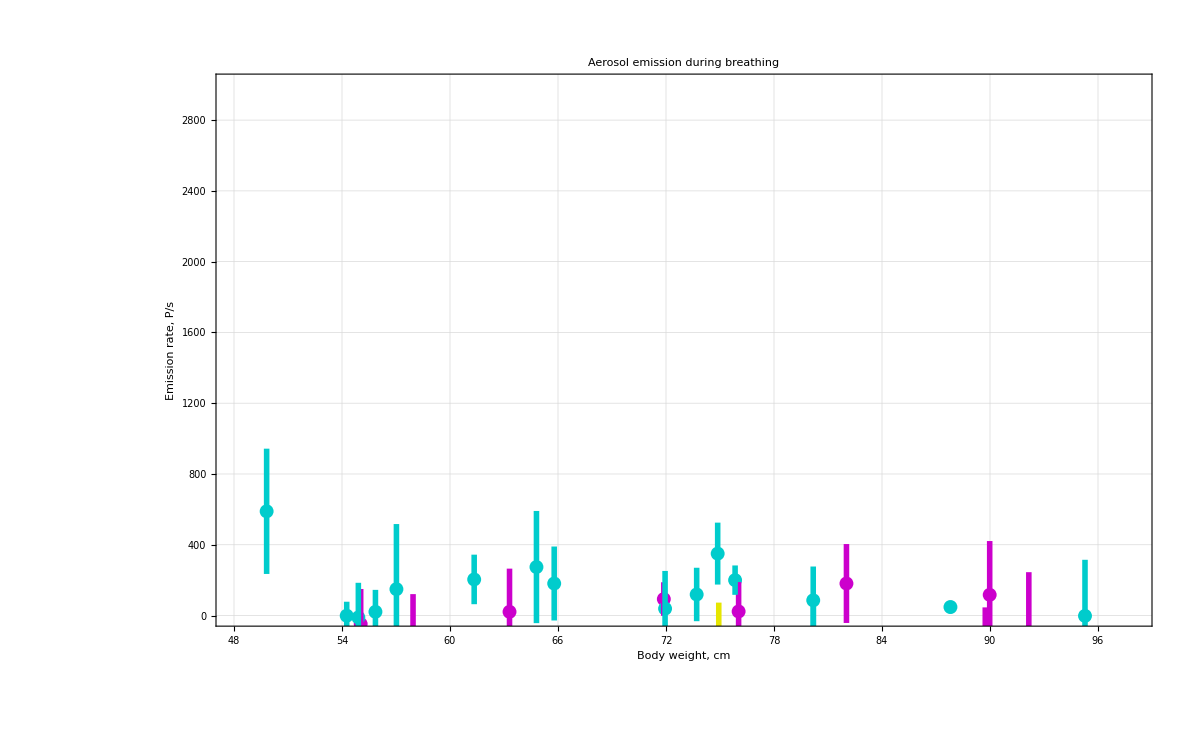

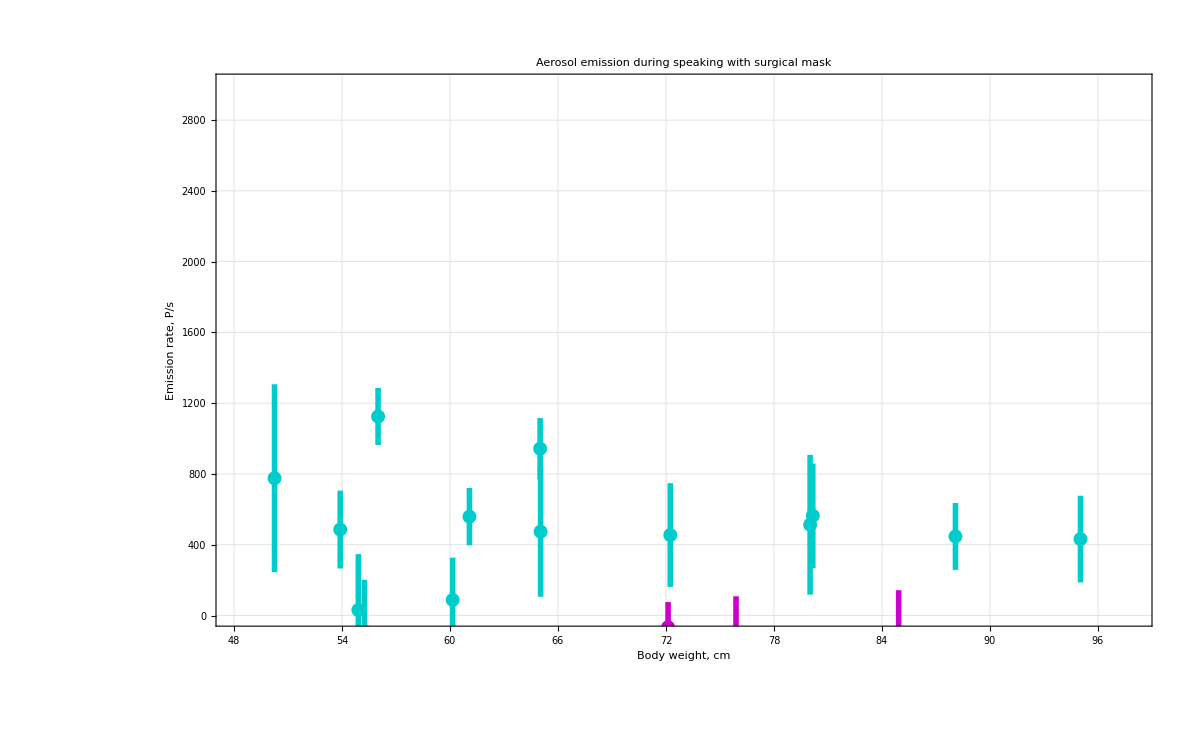

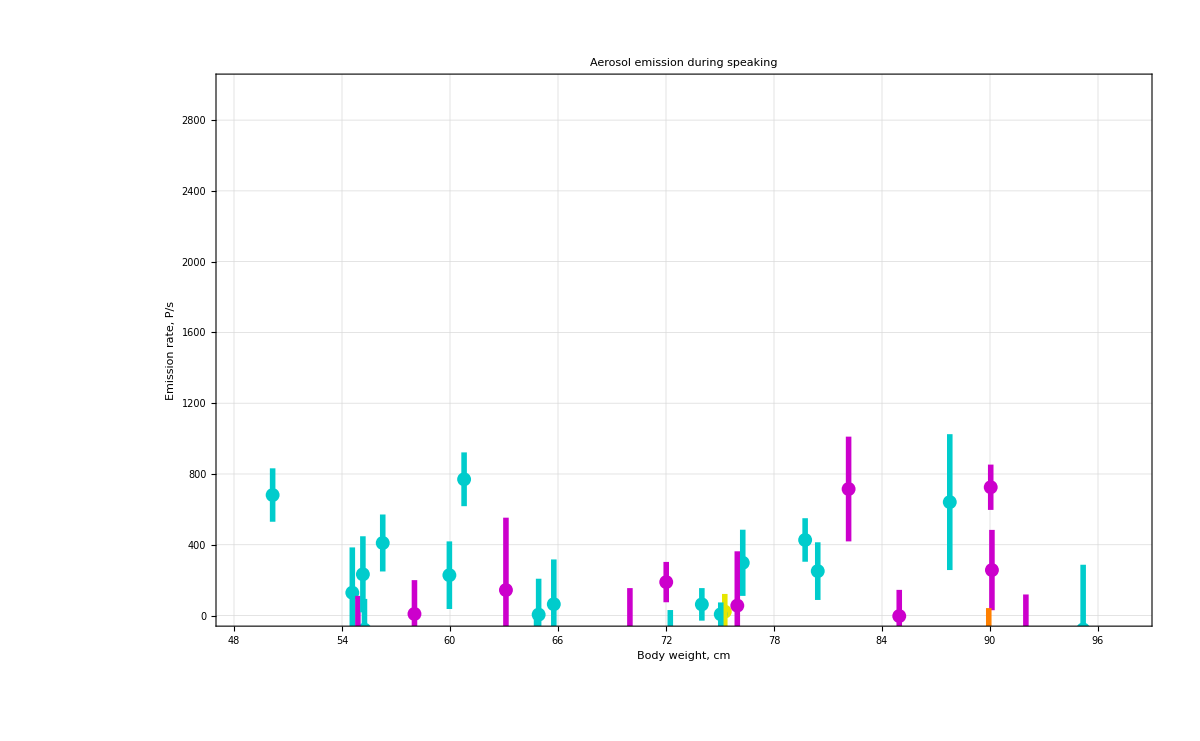

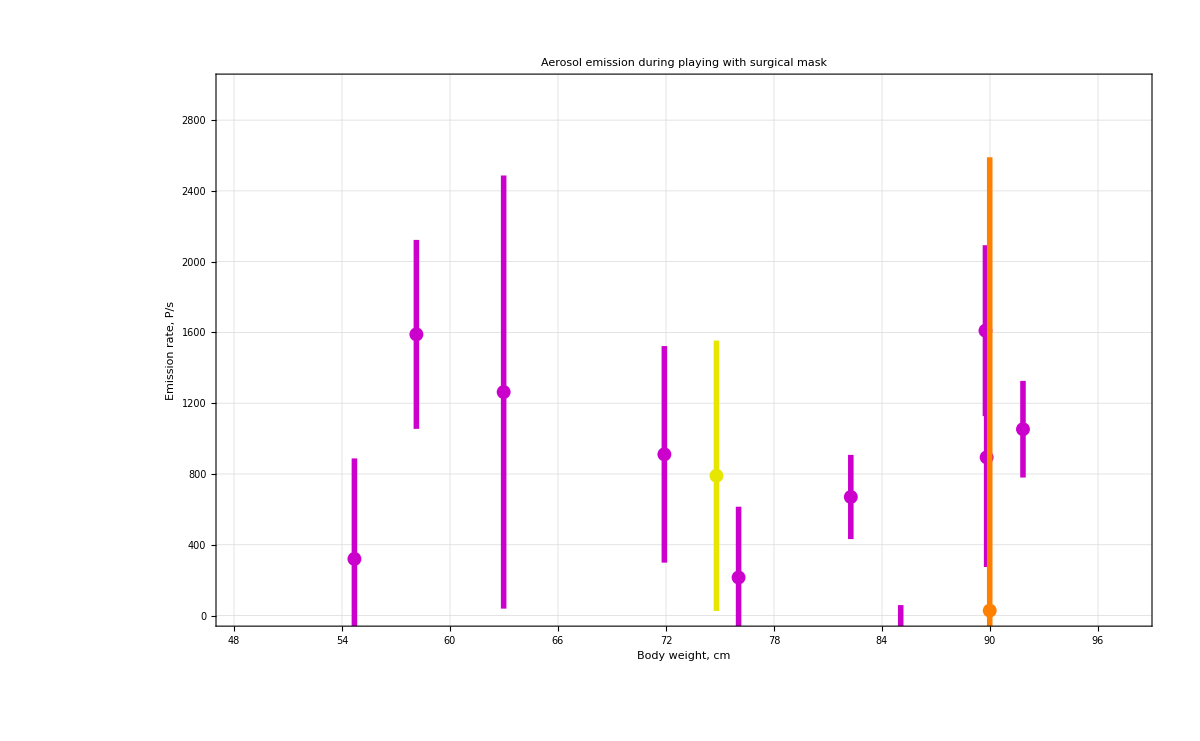

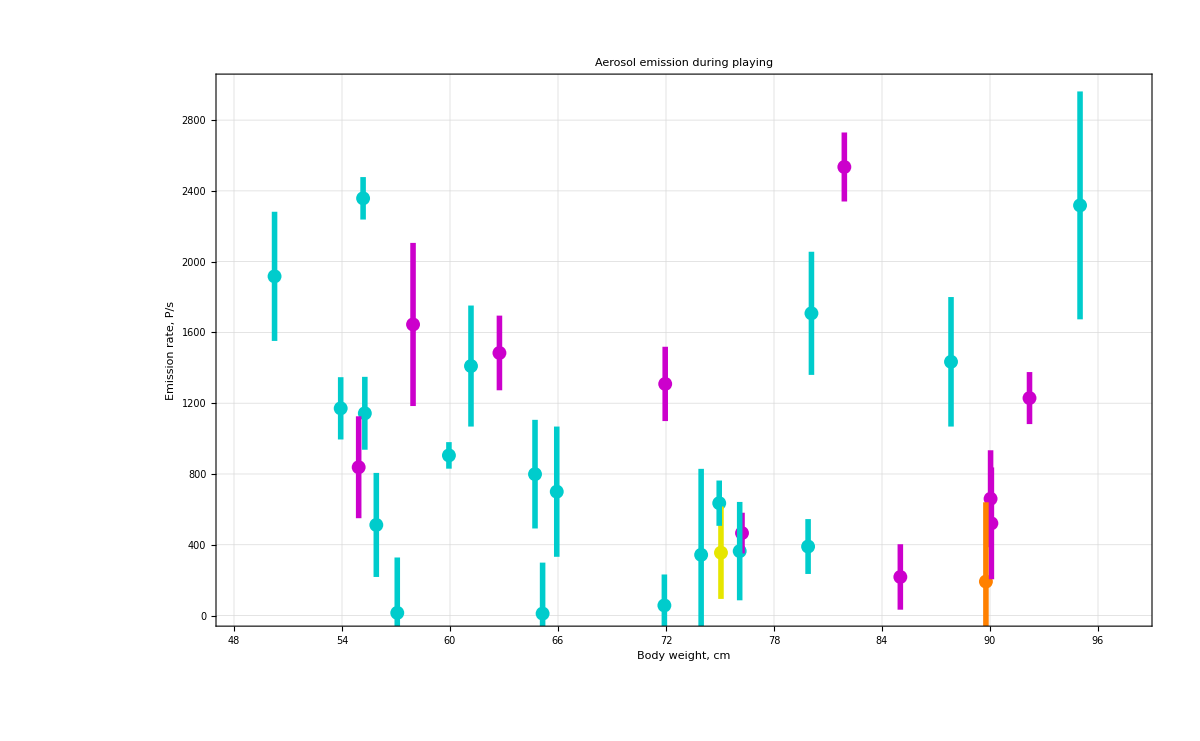

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Breathing_Emissionsrate (P-s)_weight.tif
C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Speaking With Surgical Mask_Emissionsrate (P-s)_weight.tif
C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Speaking_Emissionsrate (P-s)_weight.tif
C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Playing With Surgical Mask_Emissionsrate (P-s)_weight.tif
C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Playing_Emissionsrate (P-s)_weight.tif

```mathematica
Column[
Map[(
Clear[G,h,t,x,y];
t = #;
G = SelectRows[Z,"Instrument",(#≠"S")&];
G = SelectRows[G,"Task",(#==t)&];
G = Drop[ExtractColumn[G,{y="Emissionsrate (P/s)","ER σ (P/s)","Proband","Instrument"}/.ToEnglish],2];
G = Transpose[G];
G[[3]] = G[[3]]/.(Rule@@@(Rest[ExtractColumn[X,{"Proband",x="weight"}]]/.ToEnglish));
G[[4]] = G[[4]]/.({
"Qu"->CMYKColor[1,0,0,0.2],
"Ob"->CMYKColor[0,1,0,0.2],
"KP"->CMYKColor[0,0,0,0.3],
"Kl"->CMYKColor[0,0,1,0.1],
"Tr"->CMYKColor[0,0.5,1,0]}/.ToEnglish);
G = Transpose[G];
G = Map[{
#[[4]],
Point[{h=#[[3]]+RandomVariate[NormalDistribution[0,0.15]],#[[1]]}],
Line[{
{h,Max[-Infinity,#[[1]]-#[[2]]]},
{h,                                  #[[1]]+#[[2]]  }}]
}&,G];
Print[
G = Graphics[
{AbsoluteThickness[  4],
AbsolutePointSize[10],
G},
AspectRatio->0.618,
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{"Body weight,  cm","Emission rate,  P/s"},
GridLines  ->Automatic,
ImageSize->1200,
LabelStyle->MyTS,
PlotLabel->StringJoin["Aerosol emission during ",ToLowerCase[t]],
PlotRange->{{48,98},{-300*0,3000}},
PlotRangeClipping->True]];
Export[
StringReplace[
StringJoin[OutPath,ConcatStringList[{t,y,x},"_"],".tif"],
{"/"->"-"}],
G])&,
Measurements]]
```

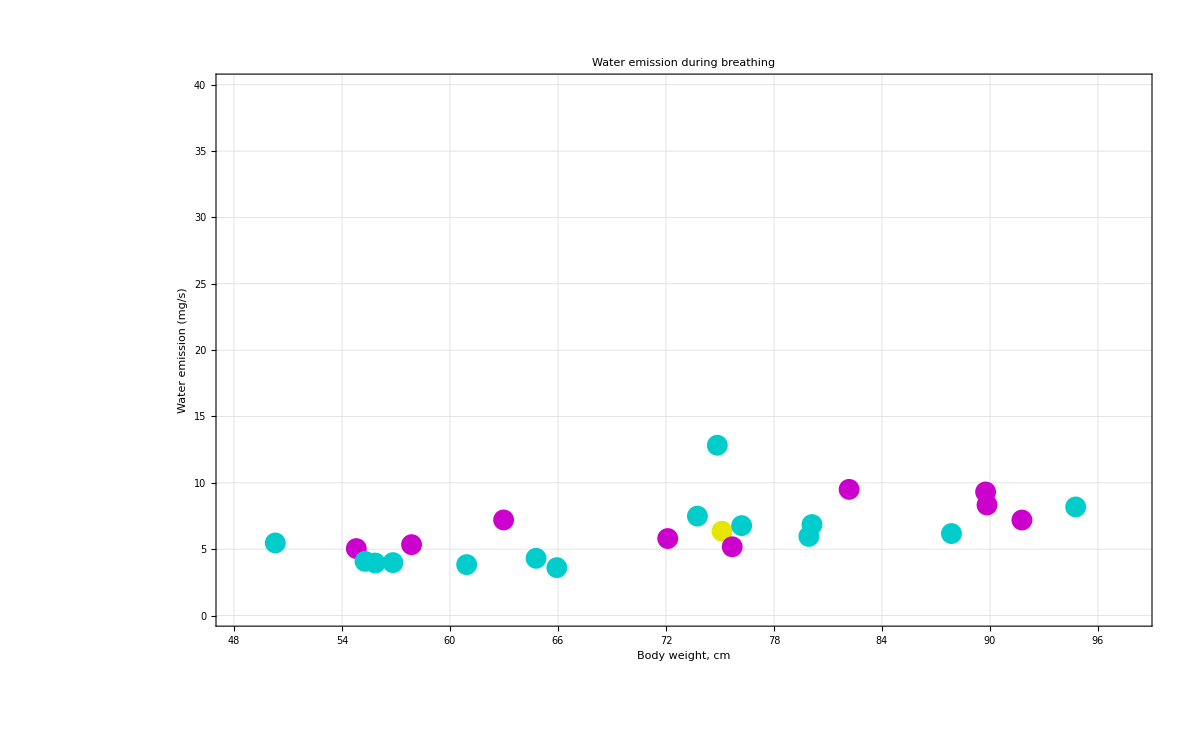

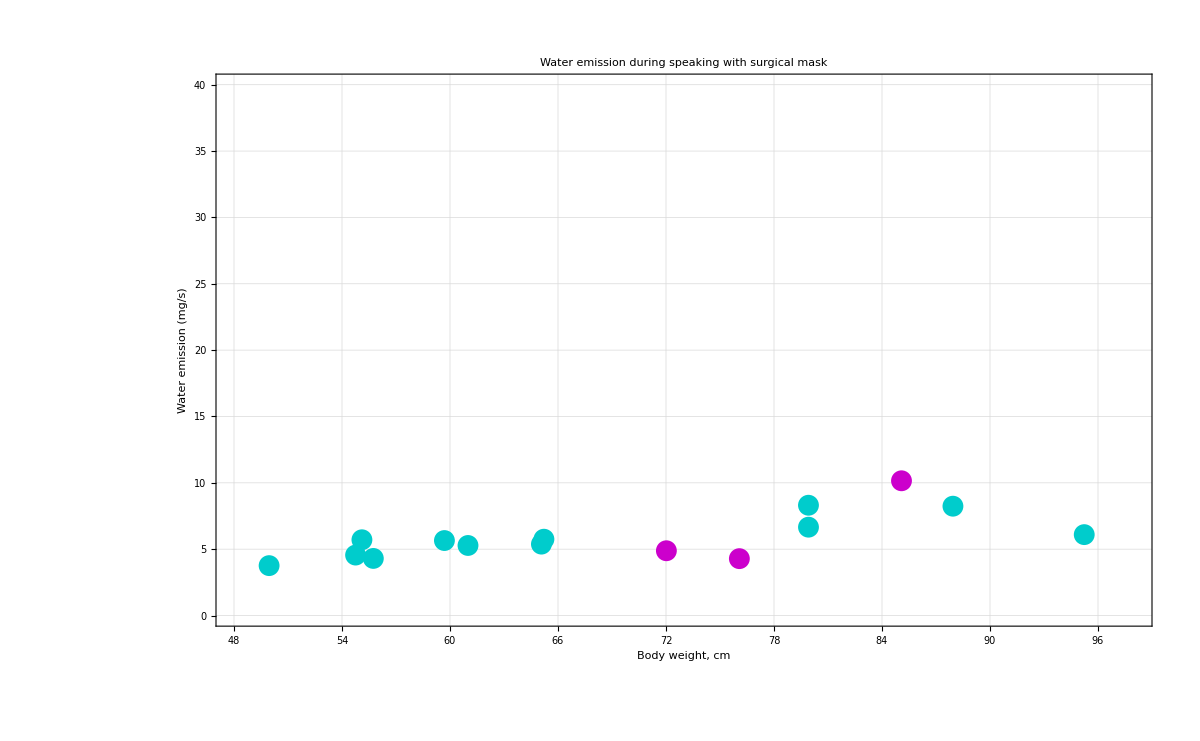

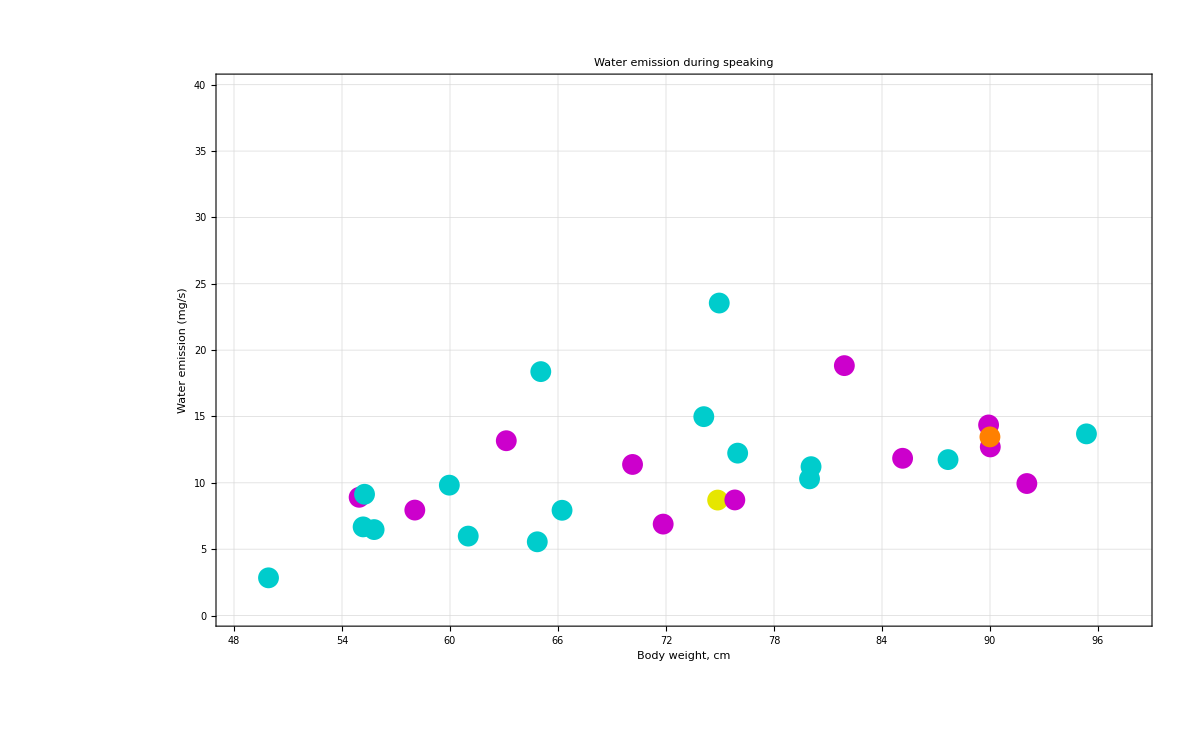

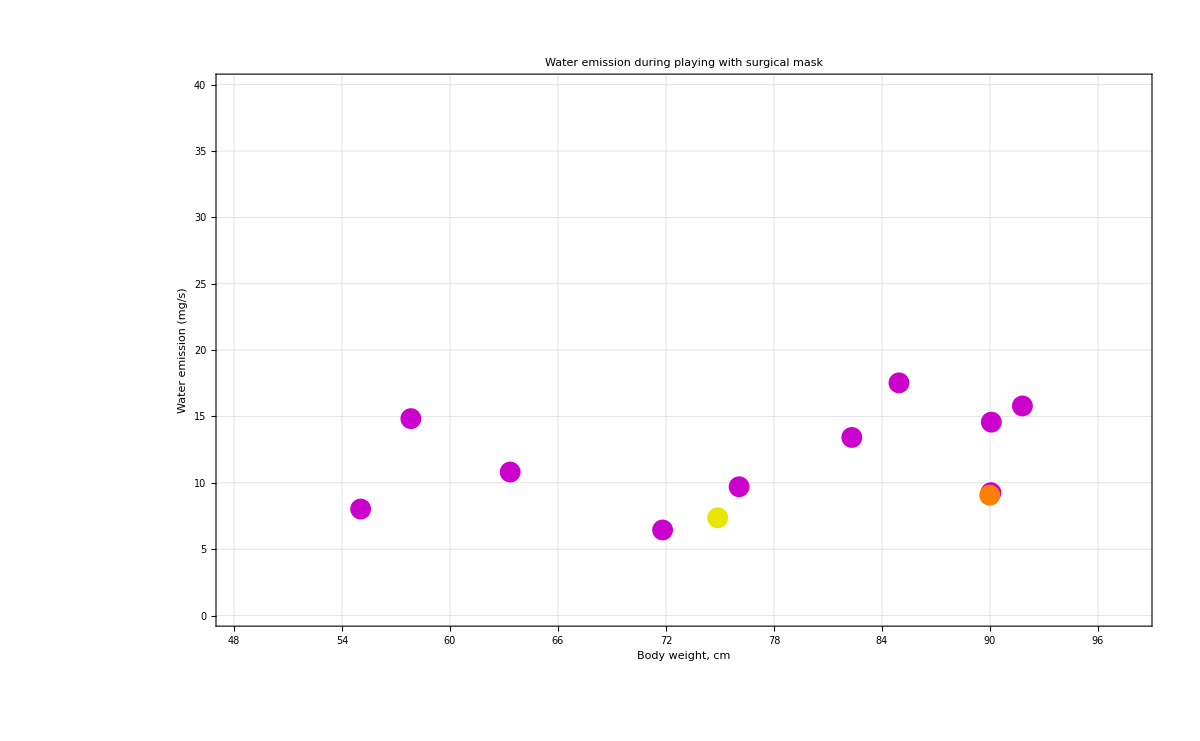

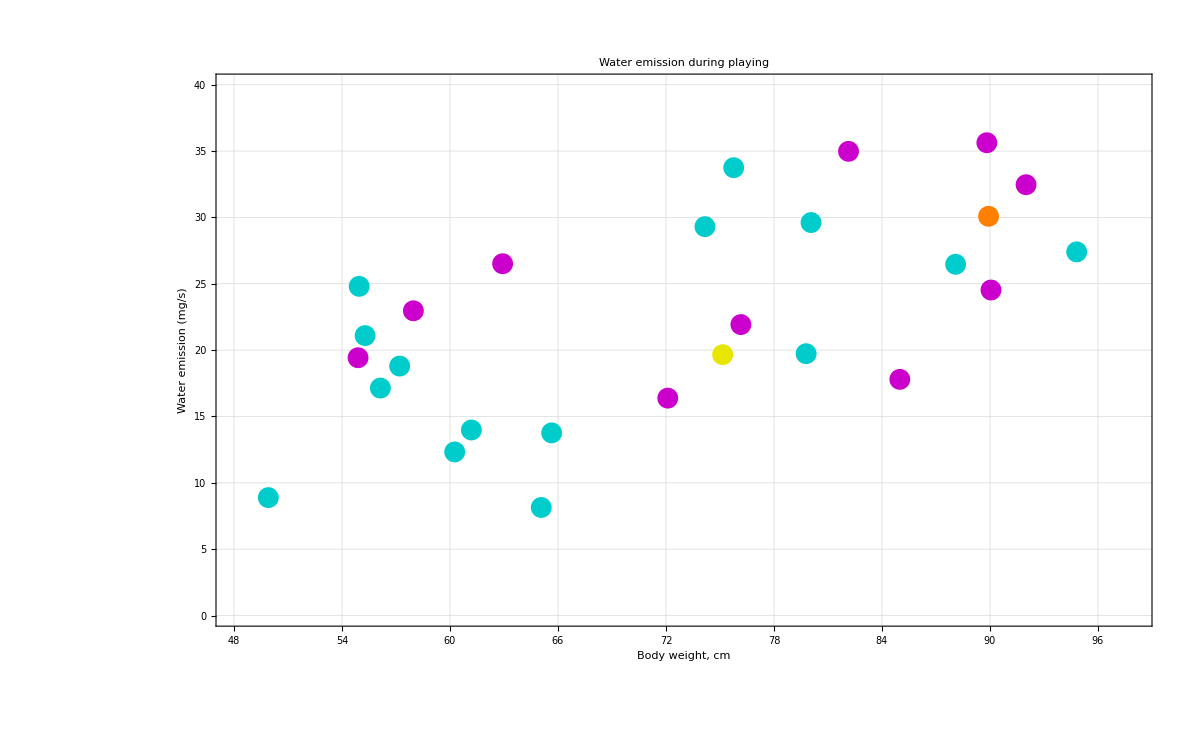

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Breathing_Water emission (mg-s)_weight.tif
C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Speaking With Surgical Mask_Water emission (mg-s)_weight.tif
C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Speaking_Water emission (mg-s)_weight.tif
C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Playing With Surgical Mask_Water emission (mg-s)_weight.tif
C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Playing_Water emission (mg-s)_weight.tif

```mathematica
Column[
Map[(
Clear[G,h,t,x,y];
t = #;
G = SelectRows[Z,"Instrument",(#≠"S")&];
G = SelectRows[G,"Task",(#==t)&];
G = Drop[ExtractColumn[G,{y="Water emission (mg/s)","Proband","Instrument"}],2];
G = Select[G,NumericQ[#[[1]]]&];
G = Transpose[G];
G[[2]] = G[[2]]/.(Rule@@@(Rest[ExtractColumn[X,{"Proband",x="weight"}]]/.ToEnglish));
G[[3]] = G[[3]]/.({
"Qu"->CMYKColor[1,0,0,0.2],
"Ob"->CMYKColor[0,1,0,0.2],
"KP"->CMYKColor[0,0,0,0.3],
"Kl"->CMYKColor[0,0,1,0.1],
"Tr"->CMYKColor[0,0.5,1,0]}/.ToEnglish);
G = Transpose[G];
G = Map[{
#[[3]],
Point[{h=#[[2]]+RandomVariate[NormalDistribution[0,0.15]],#[[1]]}]
}&,G];
Print[
G = Graphics[
{AbsolutePointSize[15],G},
AspectRatio->0.618,
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{"Body weight,  cm",y},
GridLines  ->Automatic,
ImageSize->1200,
LabelStyle->MyTS,
PlotLabel->StringJoin["Water emission during ",ToLowerCase[t]],
PlotRange->{{48,98},{0,40}},
PlotRangeClipping->True]];
Export[
StringReplace[
StringJoin[OutPath,ConcatStringList[{t,y,x},"_"],".tif"],
{"/"->"-"}],
G])&,
Measurements]]
```